by Rudolf Oldenbourg, MBL, version August 2020

## Object space graphics with LF ray locations, March 2019

### Initialization

```mathematica
(*Parameters*)
(*The typical size of the object space is 250 x 700 x 700 µm^3*)
(*possible values for voxPitch: 50,25,10,4,1.75,0.875,0.4375*)
voxPitch=25.;(*voxPitch is the side length in micron of a cubic voxel in object space and of a square cell of the entrance and exit face*)
If[OddQ[voxNrX=Round[250/voxPitch]],,voxNrX=voxNrX+1]; (*voxNrX is the number of voxels along the x-axis side of the object cube. An odd number will put the Center of a voxel in the center of object space*)
If[OddQ[voxNrYZ=Round[700/voxPitch]],,voxNrYZ=voxNrYZ+1]; (*voxNrYZ is the number of voxels along the y- and z-axis side of the object cube An odd number will put the Center of a voxel in the center of object space*)
voxCtr={voxNrX*voxPitch/2,voxNrYZ*voxPitch/2,voxNrYZ*voxPitch/2};(*voxCtr is the location in object space on which all camera rays converge*)
magnObj=60;  (*magnification of objective lens*)
naObj=1.2;     (*naObj is NA of objective lens*)
nMedium=1.33;  (*nMedium is the refractive index of the medium in object space*)
nrCamPix=16;  (*nrCamPix is the number of camera pixels behind a lenslet in the horizontal and vertical direction*)
			(*0≤i≤nrCamPix and 0≤j≤nrCamPix span the plane of camera pixels, with {i,j} Reals*)
			(*Integers {i,j} count the pixels. {0.5,0.5} is the center location of pixel {1,1}*)
camPixPitch=6.5;  (*size of camera pixels in micron*)
µLensCtr={8,8};  (*microLens center position in camera pixels*)
µLensPitch=nrCamPix*camPixPitch/magnObj;  (*µLens pitch in object space*)
rNA =7.7;  (*rNA is the radius of the edge of the objective lens aperture in camera pixels*)
(*only in Aug 2020, I became aware that the actual edge radius for the 60x/1.2NA and the Orca-Flash4 camera is rNA=7.7, not 7.2*)

(*Graphics objects*)
(*The entrance face is where rays enter object space. The face is in the y-z plane*)
entranceFaceGraphics:={
	Table[Line[{{0,1,0}*voxPitch*i,{0,1,0}*voxPitch*i+{0,0,1}*voxPitch*voxNrYZ}],{i,0,voxNrYZ}],
	Table[Line[{{0,0,1}*voxPitch*i,{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*voxNrYZ}],{i,0,voxNrYZ}]
}
(*The exit face is where rays exit object space. The face is in the y-z plane*)
exitFaceGraphics:={
	Table[Line[{{0,1,0}*voxPitch*i+{1,0,0}*voxPitch*voxNrX,{0,1,0}*voxPitch*i+{0,0,1}*voxPitch*voxNrYZ+{1,0,0}*voxPitch*voxNrX}],{i,0,voxNrYZ}],
	Table[Line[{{0,0,1}*voxPitch*i+{1,0,0}*voxPitch*voxNrX,{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*voxNrYZ+{1,0,0}*voxPitch*voxNrX}],{i,0,voxNrYZ}]
}

(*object cube*)
objectCubeGraphics:={
	Table[Line[{{0,1,0}*voxPitch*i+{1,0,0}*voxPitch*j,{0,1,0}*voxPitch*i+{0,0,1}*voxPitch*voxNrYZ+{1,0,0}*voxPitch*j}],{i,0,voxNrYZ},{j,voxNrX-1}],
	Table[Line[{{0,0,1}*voxPitch*i+{1,0,0}*voxPitch*j,{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*voxNrYZ+{1,0,0}*voxPitch*j}],{i,0,voxNrYZ},{j,voxNrX-1}],
	Table[Line[{{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*j,{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*j+{1,0,0}*voxPitch*voxNrX}],{i,0,voxNrYZ},{j,0,voxNrYZ}]
}

(*The list camPixRays[[i,j]] holds values for azimuth and tilt angles in object space for rays originating in camera pixels {i,j} behind a single lenslet*)
(*The computation implements the sine condition for points in the back focal plane of the objective lens*)
(*Making this a delayed assignment slows down the computation tremendously*)
(*Angle values need to be converted and rounded to integer degrees, otherwise later the test for all members of mP and iL having equal length fails for all voxPitch values. I don't know why!*)
camPixRays=Table[If[(tmp=Sqrt[(i-0.5-µLensCtr[[1]])^2+(j-0.5-µLensCtr[[2]])^2])>rNA,{Null},
	{ArcTan[i-0.5-µLensCtr[[1]],j-0.5-µLensCtr[[2]]]/Degree,ArcSin[tmp/rNA*naObj/nMedium]/Degree}//Round],{i,nrCamPix},{j,nrCamPix}];

(*2D line grid representing camera pixel array behind one microlens*)
camPixels2D:={
	Table[Line[{{1,0}*i,{1,0}*i+{0,1}*nrCamPix}],{i,0,nrCamPix}],
	Table[Line[{{0,1}*i,{0,1}*i+{1,0}*nrCamPix}],{i,0,nrCamPix}],
	Table[Text[{i,j},{(i-0.5),(j-0.5)}],{i,nrCamPix},{j,nrCamPix}]
}

(*2D line grid representing entrance face of rays that traverse object space*)
entranceFace2D:={
	Table[Line[{{1,0}*voxPitch*i,{1,0}*voxPitch*i+{0,1}*voxPitch*voxNrYZ}],{i,0,voxNrYZ}],
	Table[Line[{{0,1}*voxPitch*i,{0,1}*voxPitch*i+{1,0}*voxPitch*voxNrYZ}],{i,0,voxNrYZ}]
}

(*The camRayEntrance list holds the positions where camera rays pass through the entrance face into the object cube*)
(*the x position of the entrance face is 0, camera rays all converge on voxCtr*)
camRayEntrance:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,voxCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+voxCtr[[2]],
		voxCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+voxCtr[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]

(*List of object space coordinates where rays enter object space. The x-position is 0*)
rayEnter=Table[camRayEntrance[[i,2]],{i,Length[camRayEntrance]}];

(*List of object space coordinates where rays exit object space. The x-position is voxPitch*voxNrX*)
rayExit=Table[rayEnter[[i]]+2(voxCtr-rayEnter[[i]]),{i,Length[rayEnter]}];

(*List of 3 unit vectors,first is in the ray direction,second and third span the plane perpendicular to the ray direction*)
(*and are parallel to the y-and z-axis after rotating the ray parallel to x-axis towards camera.*)
(*All three unit vectors are orthogonal to each other.*)
(*rayUnitVectors[[rayNr]]={{rayDirX,rayDirY,rayDirZ},{rayPolYX,rayPolYY,rayPolYZ},{rayPolZX,rayPolZY,rayPolZZ}}*)
rayUnitVectors=Table[{tmp=rayExit[[rayNr]]-rayEnter[[rayNr]];tmp2=Inverse[RotationMatrix[{tmp,{1,0,0}}]];tmp/Norm[tmp],
					tmp2.{0,1,0},tmp2.{0,0,1}},{rayNr,Length[rayEnter]}];

(*initialization of array of tomographic images behind microlens array (camArray)*)
camArray=Table[0,{i,nrCamPix},{j,nrCamPix}];
camArrayY=Table[0,{i,nrCamPix},{j,nrCamPix}];
camArrayZ=Table[0,{i,nrCamPix},{j,nrCamPix}];

voxPitchList={voxPitch,voxPitch,voxPitch};
voxNrList={voxNrX,voxNrYZ,voxNrYZ};
```

### Graphics

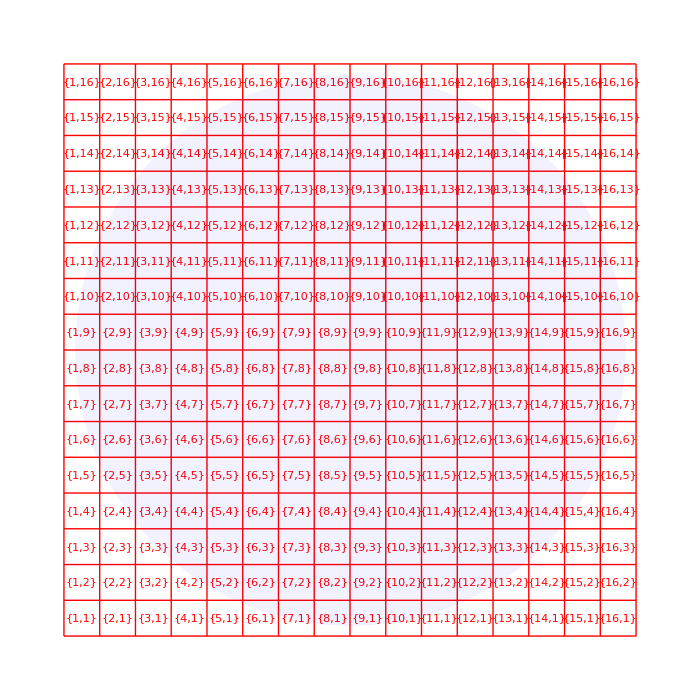

```mathematica
Graphics[{Red,camPixels2D,Blue,Opacity[0.05],Disk[µLensCtr,rNA]},ImageSize->700]
```

```mathematica
Length[camRayEntrance]
```

188

voxPitch = 25.

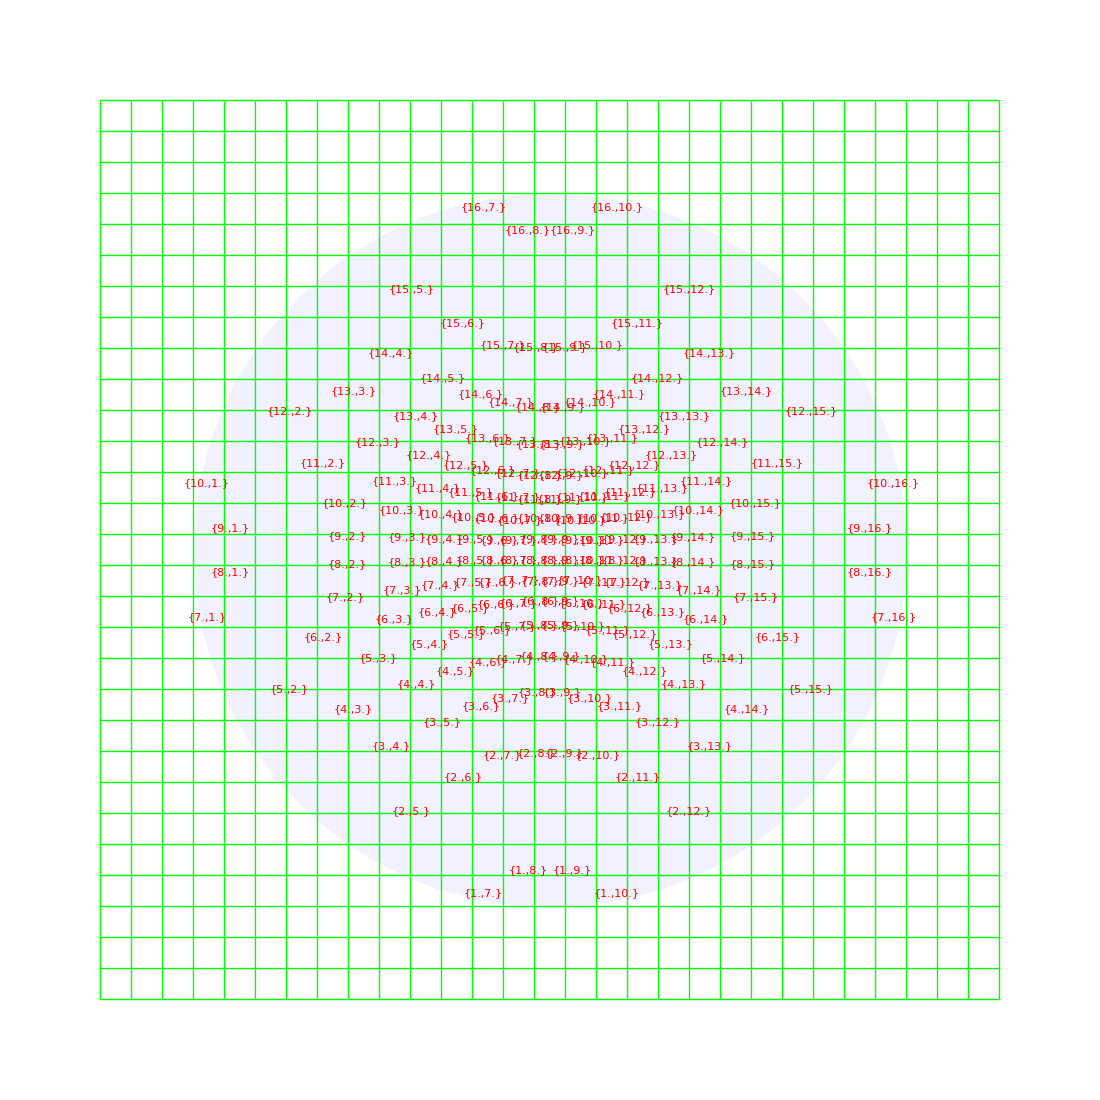

```mathematica
(*Ray positions in Entrance Face, Text shows the indices in camera pixel array*)
Print["voxPitch = ",voxPitch];
Graphics[{Blue,Opacity[0.05],Disk[Drop[voxCtr,1],voxCtr[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2D,
			Red,Table[Text[camRayEntrance[[i,1]],Drop[camRayEntrance[[i,2]],1]],{i,Length[camRayEntrance]}]},
	PlotRange->All,ImageSize->1100]
```

voxPitch = 25.

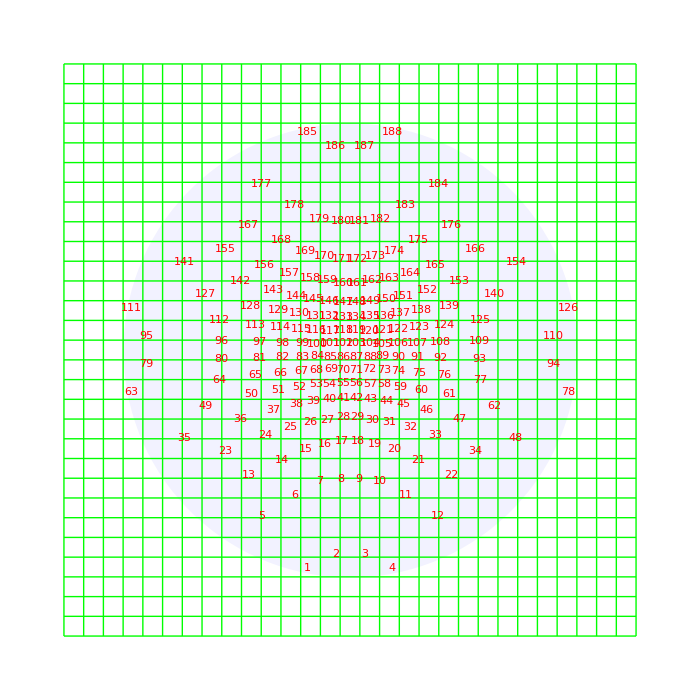

```mathematica
(*Ray positions in Entrance Face, Text shows the ray number*)
Print["voxPitch = ",voxPitch];
Graphics[{Blue,Opacity[0.05],Disk[Drop[voxCtr,1],voxCtr[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2D,
			Red,Table[Text[i,Drop[camRayEntrance[[i,2]],1]],{i,Length[camRayEntrance]}]},
	PlotRange->All,ImageSize->700]
```

voxPitch = 25.

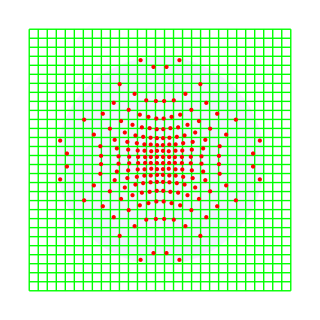

```mathematica
(*Ray positions in Entrance Face*)
Print["voxPitch = ",voxPitch];
Graphics[{Blue,Opacity[0.05],Disk[Drop[voxCtr,1],voxCtr[[1]]Tan[ArcSin[naObj/nMedium]]],
			Green,Opacity[1],entranceFace2D,
			PointSize[Large],Red,Table[Point[Drop[camRayEntrance[[i,2]],1]],{i,Length[camRayEntrance]}]},
	PlotRange->All]
```

```mathematica
rayNr=188;
Print["voxPitch = ",voxPitch];
Graphics3D[{
	Opacity[0.2],Magenta,
	objectCubeGraphics,
	Blue,Opacity[0.02],
	EdgeForm[],Cylinder[{{0,voxCtr[[2]],voxCtr[[3]]},{0.1,voxCtr[[2]],voxCtr[[3]]}},voxCtr[[1]]Tan[ArcSin[naObj/nMedium]]],
	Opacity[1],Green,
	entranceFaceGraphics,
	exitFaceGraphics,
	Opacity[1],Blue,Thick,
	Arrow[{rayEnter[[rayNr]],rayExit[[rayNr]]}] 
},Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->400]
```

voxPitch = 25.

-Graphics3D-

## Siddon algorithm for ray tracing, March 2019 Siddon, R. L. (1985). Fast calculation of the exact radiological path for a three-dimensional CT array. Med. Phys., 12(2):252-5. http://dx.doi.org/10.1118/1.595715

### Initialization

#### Python Implementation (Nathaniel Holderman, UChicago)

# Python code
#  siddon.py
# Implemented by Nathaniel Holderman 2018
from math import floor, ceil, sqrt

def raytrace (x1, y1, z1, x2, y2, z2, dx, dy, dz, pix_numx, pix_numy, pix_numz) : #first, compute starting and ending parametric values in each dimension
if (x2 - x1) != 0 : ax_ 0 = -x1/(x2 - x1)
ax_N = (pix_numx*dx - x1)/(x2 - x1)
else : ax_ 0 = 0
ax_N = 1
if (y2 - y1) != 0 : ay_ 0 = -y1/(y2 - y1)
ay_N = (pix_numy*dy - y1)/(y2 - y1)
else : ay_ 0 = 0
ay_N = 1
if (z2 - z1) != 0 : az_ 0 = -z1/(z2 - z1)
az_N = (pix_numz - z1)/(z2 - z1)
else : az_ 0 = 0
az_N = 1

#then calculate absolute max and min parametric values
a_min = max (0, min (ax_ 0, ax_N), min (ay_ 0, ay_N), min (az_ 0, az_N))
a_max = min (1, max (ax_ 0, ax_N), max (ay_ 0, ay_N), max (az_ 0, az_N))

#now find range of indices corresponding to max/min a values
if (x2 - x1) >= 0 : i_min = ceil (pix_numx - (pix_numx*dx - a_min*(x2 - x1) - x1)/dx)
i_max = floor ( 1 + (x1 + a_max*(x2 - x1))/dx)										The "1 + “ is missing from Nathaniel Holderman’s original code
elif (x2 - x1) < 0 : i_min = ceil (pix_numx - (pix_numx*dx - a_max*(x2 - x1) - x1)/dx)
i_max = floor ( 1 + (x1 + a_min*(x2 - x1))/dx)

if (y2 - y1) >= 0 : j_min = ceil (pix_numy - (pix_numy*dy - a_min*(y2 - y1) - y1)/dy)
j_max = floor ( 1 + (y1 + a_max*(y2 - y1))/dy)
elif (y2 - y1) < 0 : j_min = ceil (pix_numy - (pix_numy*dy - a_max*(y2 - y1) - y1)/dy)
j_max = floor ( 1 + (y1 + a_min*(y2 - y1))/dy)

if (z2 - z1) >= 0 : k_min = ceil (pix_numz - (pix_numz*dz - a_min*(z2 - z1) - z1)/dz)
k_max = floor ( 1 + (z1 + a_max*(z2 - z1))/dz)
elif (z2 - z1) < 0 : k_min = ceil (pix_numz - (pix_numz*dz - a_max*(z2 - z1) - z1)/dz)
k_max = floor ( 1 + (z1 + a_min*(z2 - z1))/dz)

#next calculate the list of parametric values for each coordinate
a_x = []
if (x2 - x1) > 0 : for i in range (i_min, i_max) : a_x.append ((i*dx - x1)/(x2 - x1))
elif (x2 - x1) < 0 : for i in range (i_min, i_max) : a_x.insert (0, (i*dx - x1)/(x2 - x1))

a_y = []
if (y2 - y1) > 0 : for j in range (j_min, j_max) : a_y.append ((j*dy - y1)/(y2 - y1))
elif (y2 - y1) < 0 : for j in range (j_min, j_max) : a_y.insert (0, (j*dy - y1)/(y2 - y1))

a_z = []
if (z2 - z1) > 0 : for k in range (k_min, k_max) : a_z.append ((k*dz - z1)/(z2 - z1))
elif (z2 - z1) < 0 : for k in range (k_min, k_max) : a_z.insert (0, (k*dz - z1)/(z2 - z1))

#finally, form the list of parametric values
a_list = [a_min] + a_x + a_y + a_z + [a_max]
a_list = list (set (a_list))
a_list.sort ()
return a_list

def midpoints (x1, y1, z1, x2, y2, z2, dx, dy, dz, pix_numx, pix_numy, pix_numz) : a_list = raytrace (x1, y1, z1, x2, y2, z2, dx, dy, dz, pix_numx, pix_numy, pix_numz)

#loop though, computing midpoints for each adjacent pair of a values for chosen coord

i_mid = []
for m in range (1, len (a_list)) : x = .5*(a_list[m] + a_list[m - 1])*(x2 - x1) + x1
y = .5*(a_list[m] + a_list[m - 1])*(y2 - y1) + y1
z = .5*(a_list[m] + a_list[m - 1])*(z2 - z1) + z1
i_mid.append ((x, y, z))
return i_mid

def intersect_length (x1, y1, z1, x2, y2, z2, dx, dy, dz, pix_numx, pix_numy, pix_numz) : a_list = raytrace (x1, y1, z1, x2, y2, z2, dx, dy, dz, pix_numx, pix_numy, pix_numz)

#find length of intersection by multiplying difference in parametric values by total ray length

lengths = []
for m in range (1, len (a_list)) : lengths.append (sqrt ((x2 - x1) ** 2 + (y2 - y1) ** 2 + (z2 - z1) ** 2)*(a_list[m] - a_list[m - 1]))
return lengths

#  test - siddon.py
from siddon import*# Assemble arguments
x1, y1, z1 = 0, 0, 0
x2, y2, z2 = 1, 1, 1
dx, dy, dz = 0.1, 0.1, 0.1
nx, ny, nz = 10, 10, 10
args = (x1, y1, z1, x2, y2, z2, dx, dy, dz, nx, ny, nz)

# Test Siddon
midpoints = midpoints (*args) lengths=intersect_length(*args) print('Midpoints:'+str([(round(x[0],3),round(x[1],3),round(x[2],3)) for x in midpoints])) print('Lengths:'+str([round(x,3) for x in lengths])) # Check lengths from math import sqrt print('Input length:'+str(sqrt((x2-x1)**2+(y2-y1)**2+(z2-z1)**2))) print('Output length:'+str(sum(lengths)))

#### Mathematica Implementation (RO)

```mathematica
(*Siddon algorithms, Mathematica implementation by Rudolf Oldenbourg, March 2019, based on Python code from Nathaniel Holderman in 2018*)
(*pixNumXIn is the number of voxels in x-direction between entrance face and front face of bounding object box. The same applies to y- and z-direction*)
(*pixNumXOut is the number of voxels in x-direction between entrance face and back face of bounding object box. The same applies to y- and z-direction*)
rayTrace[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
(*Catch[*)Module[{ax={},ax0,axN,ay={},ay0,ayN,az={},az0,azN,aMin,aMax,iMin,iMax,jMin,jMax,kMin,kMax},
(*first,compute starting and ending parametric values in each dimension*)
		If[x2-x1≠0,ax0=(pixNumXIn dx-x1)/(x2-x1);axN=(pixNumXOut*dx-x1)/(x2-x1),ax0=0.;axN=1.];
		If[y2-y1≠0,ay0=(pixNumYIn dy-y1)/(y2-y1);ayN=(pixNumYOut*dy-y1)/(y2-y1),ay0=0.;ayN=1.];
		If[z2-z1≠0,az0=(pixNumZIn dz-z1)/(z2-z1);azN=(pixNumZOut*dz-z1)/(z2-z1),az0=0.;azN=1.];
(*Print["ax0=",ax0,", axN=",axN,", ay0=",ay0,", ayN=",ayN,", az0=",az0,", azN=",azN];*)
(*then calculate absolute max and min parametric values*)
		aMin=Max[0.,Min[ax0,axN],Min[ay0,ayN],Min[az0,azN]];
		aMax=Min[1.,Max[ax0,axN],Max[ay0,ayN],Max[az0,azN]];
(*Print["aMin=",aMin,", aMax=",aMax];*)
(*now find range of indices corresponding to max/min a values*)
(*in this application, (x2-x1) is always greater zero*)
(*		iMin=Ceiling[(aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];*)
		iMin=Ceiling[pixNumXOut-(pixNumXOut*dx-aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];
		If[(y2-y1)≥0,
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMin*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMax*(y2-y1))/dy],
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMax*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMin*(y2-y1))/dy]];
		If[(z2-z1)≥0,
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMin*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMax*(z2-z1))/dz],
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMax*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMin*(z2-z1))/dz]];
(*Print["iMin=",iMin,", iMax=",iMax,", jMin=",jMin,", jMax=",jMax,", kMin=",kMin,", kMax=",kMax];*)
(*next calculate the list of parametric values for each coordinate*)
		For [i=iMin,i<iMax,i++,ax=Append[ax,(i*dx-x1)/(x2-x1)]];
		If [y2-y1>0,For [j=jMin,j<jMax,j++,ay=Append[ay,(j*dy-y1)/(y2-y1)]]];
		If [y2-y1<0,For [j=jMin,j<jMax,j++,ay=Prepend[ay,(j*dy-y1)/(y2-y1)]]];
		If [z2-z1>0,For [k=kMin,k<kMax,k++,az=Append[az,(k*dz-z1)/(z2-z1)]]];
		If [z2-z1<0,For [k=kMin,k<kMax,k++,az=Prepend[az,(k*dz-z1)/(z2-z1)]]];
(*Print["ax=",ax];
Print["ay=",ay];
Print["az=",az];
Throw["thrown"];*)
(*finally,form the list of parametric values*)
		Union[{aMin},ax,ay,az,{aMax}]]
(*	]*)

midPoints[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,x,y,z,iMid},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*loop through, computing midpoints for each adjacent pair of a values for chosen coord*)
		iMid={};
		For[m =2,m≤Length[aList],m++,
			x=.5*(aList[[m]]+aList[[m-1]])*(x2-x1)+x1;
			y=.5*(aList[[m]]+aList[[m-1]])*(y2-y1)+y1;
			z=.5*(aList[[m]]+aList[[m-1]])*(z2-z1)+z1;
			iMid=Append[iMid,{x,y,z}]];
	iMid]

intersectLength[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,lengths},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*find length of intersection by multiplying difference in parametric values by total ray length*)
		lengths={};
		For[m =2,m≤Length[aList],m++,
			lengths=Append[lengths,Sqrt[(x2-x1)^2+(y2-y1)^2+(z2-z1)^2]*(aList[[m]]-aList[[m-1]])]];
	lengths]
```

### Testing

```mathematica
voxPitch
```

0.577778

```mathematica
µLensPitch
```

1.73333

```mathematica
voxCtr
```

{125.667,351.,351.}

```mathematica
rayEnter[[17]]  (*17,28,137,148*)
```

{0.,159.329,195.788}

```mathematica
rayExit[[17]]
```

{251.333,542.671,506.212}

```mathematica
(rayExit[[17]]+rayEnter[[17]])/2
```

{125.667,351.,351.}

```mathematica
voxNrList
```

{145,405,405}

```mathematica
smp=guv[15µLensPitch,voxPitch];
```

```mathematica
smp[[2]]/voxPitch
```

{93.,93.,93.}

```mathematica
smp[[1,4]]/voxPitch
```

45.5

```mathematica
Transpose[{voxCtr-smp[[2]]/2,voxCtr+smp[[2]]/2}]/voxPitch
```

{{170.,263.},{560.,653.},{560.,653.}}

```mathematica
(*test-siddon*)
rayNr=89(*17,28,137,148*)
voxPitchList
voxCtr
smp[[2]]/voxPitch
smp[[1,4]]/µLensPitch
voxNrListTest=Transpose[{voxCtr-smp[[2]]/2,voxCtr+smp[[2]]/2}]/voxPitch
rT=rayTrace[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxNrListTest]
mP=midPoints[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxNrListTest]
iL=intersectLength[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxNrListTest]
```

89

{0.577778,0.577778,0.577778}

{125.089,350.422,350.422}

{93.,93.,93.}

15.1667

{{170.,263.},{560.,653.},{560.,653.}}

{0.39261,0.394919,0.397229,0.399538,0.401848,0.404157,0.406467,0.408215,0.408215,0.408776,0.411085,0.413395,0.415704,0.418014,0.420323,0.422633,0.424942,0.427252,0.429561,0.431871,0.43418,0.43649,0.438799,0.441109,0.443418,0.444929,0.444929,0.445727,0.448037,0.450346,0.452656,0.454965,0.457275,0.459584,0.461894,0.464203,0.466513,0.468822,0.471132,0.473441,0.475751,0.47806,0.48037,0.481643,0.481643,0.482679,0.484988,0.487298,0.489607,0.491917,0.494226,0.496536,0.498845,0.501155,0.503464,0.505774,0.508083,0.510393,0.512702,0.515012,0.517321,0.518357,0.518357,0.51963,0.52194,0.524249,0.526559,0.528868,0.531178,0.533487,0.535797,0.538106,0.540416,0.542725,0.545035,0.547344,0.549654,0.551963,0.554273,0.555071,0.555071,0.556582,0.558891,0.561201,0.56351,0.56582,0.568129,0.570439,0.572748,0.575058,0.577367,0.579677,0.581986,0.584296,0.586605,0.588915,0.591224,0.591785,0.591785,0.593533,0.595843,0.598152,0.600462,0.602771,0.605081,0.60739}

{{98.5111,348.75,352.094},{99.0889,348.787,352.058},{99.6667,348.823,352.021},{100.244,348.859,351.985},{100.822,348.896,351.949},{101.4,348.932,351.912},{101.908,348.964,351.88},{102.126,348.978,351.867},{102.196,348.982,351.862},{102.556,349.005,351.84},{103.133,349.041,351.803},{103.711,349.077,351.767},{104.289,349.114,351.731},{104.867,349.15,351.694},{105.444,349.187,351.658},{106.022,349.223,351.622},{106.6,349.259,351.585},{107.178,349.296,351.549},{107.756,349.332,351.513},{108.333,349.368,351.476},{108.911,349.405,351.44},{109.489,349.441,351.404},{110.067,349.477,351.367},{110.644,349.514,351.331},{111.122,349.544,351.301},{111.311,349.556,351.289},{111.411,349.562,351.283},{111.8,349.586,351.258},{112.378,349.623,351.222},{112.956,349.659,351.185},{113.533,349.695,351.149},{114.111,349.732,351.113},{114.689,349.768,351.076},{115.267,349.804,351.04},{115.844,349.841,351.004},{116.422,349.877,350.967},{117.,349.913,350.931},{117.578,349.95,350.895},{118.156,349.986,350.858},{118.733,350.022,350.822},{119.311,350.059,350.786},{119.889,350.095,350.749},{120.337,350.123,350.721},{120.496,350.133,350.711},{120.626,350.141,350.703},{121.044,350.168,350.677},{121.622,350.204,350.64},{122.2,350.24,350.604},{122.778,350.277,350.568},{123.356,350.313,350.531},{123.933,350.35,350.495},{124.511,350.386,350.459},{125.089,350.422,350.422},{125.667,350.459,350.386},{126.244,350.495,350.35},{126.822,350.531,350.313},{127.4,350.568,350.277},{127.978,350.604,350.24},{128.556,350.64,350.204},{129.133,350.677,350.168},{129.552,350.703,350.141},{129.681,350.711,350.133},{129.841,350.721,350.123},{130.289,350.749,350.095},{130.867,350.786,350.059},{131.444,350.822,350.022},{132.022,350.858,349.986},{132.6,350.895,349.95},{133.178,350.931,349.913},{133.756,350.967,349.877},{134.333,351.004,349.841},{134.911,351.04,349.804},{135.489,351.076,349.768},{136.067,351.113,349.732},{136.644,351.149,349.695},{137.222,351.185,349.659},{137.8,351.222,349.623},{138.378,351.258,349.586},{138.767,351.283,349.562},{138.866,351.289,349.556},{139.055,351.301,349.544},{139.533,351.331,349.514},{140.111,351.367,349.477},{140.689,351.404,349.441},{141.267,351.44,349.405},{141.844,351.476,349.368},{142.422,351.513,349.332},{143.,351.549,349.296},{143.578,351.585,349.259},{144.156,351.622,349.223},{144.733,351.658,349.187},{145.311,351.694,349.15},{145.889,351.731,349.114},{146.467,351.767,349.077},{147.044,351.803,349.041},{147.622,351.84,349.005},{147.981,351.862,348.982},{148.052,351.867,348.978},{148.27,351.88,348.964},{148.778,351.912,348.932},{149.356,351.949,348.896},{149.933,351.985,348.859},{150.511,352.021,348.823},{151.089,352.058,348.787},{151.667,352.094,348.75}}

{0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.439076,9.06263×10^-13,0.140983,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.379458,9.06263×10^-13,0.200602,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.319839,9.06263×10^-13,0.26022,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.26022,9.20205×10^-13,0.319839,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.200602,8.9232×10^-13,0.379458,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059,0.140983,9.20205×10^-13,0.439076,0.580059,0.580059,0.580059,0.580059,0.580059,0.580059}

89
{1.73333,1.73333,1.73333}
{125.667,351.,351.}
{26.8667,26.8667,26.8667}
15.5
{{56.,89.},{186.,219.},{186.,219.}}

```mathematica
Length[rT]
Length[mP]
Length[iL]
```

106

105

105

```mathematica
voxCtr
```

{125.667,351.,351.}

## Ray tracing in object space, isotropic and anisotropic fluorescence

#### Notes All distances in micron Expand for more notes

In contrast to the Oct. 2018 implementation,  now one corner of the object cube is at the origin {0, 0, 0}, and voxel positions extend only in the positive x, y, and z  directions.
This is because the Siddon algorithm seems to require only positive x,y,z values, starting with one cube corner at the origin.
A volume element dimension in x, y, and z is equal to voxPitch.
The dimensions of the object cube are defined by the number of voxels along the x-axis (voxNrX, x-axis is the microscope axis) and along the y- and z-axis (voxNrYZ). Both, voxNrX and voxNrYZ need to be odd to place a voxel center into the center of the object volume

Sample objects are defined in their own sample cube, which also has an odd number of voxels (same size voxPitch) along the x-, y-, z-directions.
The center of an object cube is in the center of a voxel.

```mathematica
(*Initialization for both, isotropic and anisotropic fluorescence*)
(*The typical size of the object space is 250 x 700 x 700 µm^3 for a 60x/1.2NA objective lens*)
voxPitch=26/15//N;(*typically = 1.7333 = 104/60, which is the µLens diameter in µm in sample space. voxPitch is the side length in micron of a cubic voxel in object space*)
```

```mathematica
If[OddQ[voxNrX=Round[250/voxPitch]],,voxNrX=voxNrX+1]; (*voxNrX is the number of voxels along the x-axis side of the object cube. An odd number will put the Center of a voxel in the center of object space*)
If[OddQ[voxNrYZ=Round[700/voxPitch]],,voxNrYZ=voxNrYZ+1]; (*voxNrYZ is the number of voxels along the y- and z-axis side of the object cube An odd number will put the Center of a voxel in the center of object space*)
voxCtr={voxNrX*voxPitch/2,voxNrYZ*voxPitch/2,voxNrYZ*voxPitch/2};(*voxCtr is the location in object space on which all camera rays converge*)
magnObj=60;  (*magnification of objective lens*)
naObj=1.2;     (*naObj is NA of objective lens; ArcSine[1.2/1.33]=64°, tilt angle of ray passing through edge of aperture*)
nMedium=1.33;  (*nMedium is the refractive index of the medium in object space*)
nrCamPix=16;  (*nrCamPix is the number of camera pixels behind a lenslet in the horizontal and vertical direction*)
			(*0≤i≤nrCamPix and 0≤j≤nrCamPix span the plane of camera pixels, with {i,j} Reals*)
			(*Integers {i,j} count the pixels. {0.5,0.5} is the center location of pixel {1,1}*)
camPixPitch=6.5;  (*size of camera pixels in micron*)
µLensCtr={8,8};  (*microLens center position in camera pixels*)
µLensPitch=If[voxPitch>26/15,voxPitch,Round[26/15/voxPitch]voxPitch];  (*µLens pitch = 1.7333 = 26/15 = 104/60µm in object space when using 60x objective lens. Make µLensPitch/voxPitch an integer*)
rNA =7.7;  (*rNA is the radius of the edge of the objective lens aperture in camera pixels; rNA = 7.7 for 60x/1.2NA objective lens and Orca-Flash4 camera*)
(*only in Aug 2020, I became aware that the actual edge radius for the 60x/1.2NA and the Orca-Flash4 camera is rNA=7.7, not 7.2*)

(*Graphics objects*)
(*The entrance face is where rays entering object space. The face is in the y-z plane*)
entranceFaceGraphics:={
	Table[Line[{{0,1,0}*voxPitch*i,{0,1,0}*voxPitch*i+{0,0,1}*voxPitch*voxNrYZ}],{i,0,voxNrYZ}],
	Table[Line[{{0,0,1}*voxPitch*i,{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*voxNrYZ}],{i,0,voxNrYZ}]
}
(*The exit face is where rays exit object space. The face is in the y-z plane*)
exitFaceGraphics:={
	Table[Line[{{0,1,0}*voxPitch*i+{1,0,0}*voxPitch*voxNrX,{0,1,0}*voxPitch*i+{0,0,1}*voxPitch*voxNrYZ+{1,0,0}*voxPitch*voxNrX}],{i,0,voxNrYZ}],
	Table[Line[{{0,0,1}*voxPitch*i+{1,0,0}*voxPitch*voxNrX,{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*voxNrYZ+{1,0,0}*voxPitch*voxNrX}],{i,0,voxNrYZ}]
}

(*object cube*)
objectCubeGraphics:={
	Table[Line[{{0,1,0}*voxPitch*i+{1,0,0}*voxPitch*j,{0,1,0}*voxPitch*i+{0,0,1}*voxPitch*voxNrYZ+{1,0,0}*voxPitch*j}],{i,0,voxNrYZ},{j,voxNrX-1}],
	Table[Line[{{0,0,1}*voxPitch*i+{1,0,0}*voxPitch*j,{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*voxNrYZ+{1,0,0}*voxPitch*j}],{i,0,voxNrYZ},{j,voxNrX-1}],
	Table[Line[{{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*j,{0,0,1}*voxPitch*i+{0,1,0}*voxPitch*j+{1,0,0}*voxPitch*voxNrX}],{i,0,voxNrYZ},{j,0,voxNrYZ}]
}

(*Ray locations in entrance face*)
(*The list camPixRays[[i,j]] holds values for azimuth and tilt angles in object space for rays originating in camera pixels {i,j} behind a single lenslet*)
(*The computation implements the sine condition for points in the back focal plane of the objective lens*)
(*Making this a delayed assignment slows down the computation tremendously*)
camPixRays=Table[If[(tmp=Sqrt[(i-0.5-µLensCtr[[1]])^2+(j-0.5-µLensCtr[[2]])^2])>rNA,{Null},
	{ArcTan[i-0.5-µLensCtr[[1]],j-0.5-µLensCtr[[2]]]/Degree,ArcSin[tmp/rNA*naObj/nMedium]/Degree}],{i,nrCamPix},{j,nrCamPix}];

(*2D line grid representing camera pixel array behind one microlens*)
camPixels2D:={
	Table[Line[{{1,0}*i,{1,0}*i+{0,1}*nrCamPix}],{i,0,nrCamPix}],
	Table[Line[{{0,1}*i,{0,1}*i+{1,0}*nrCamPix}],{i,0,nrCamPix}],
	Table[Text[{i,j},{(i-0.5),(j-0.5)}],{i,nrCamPix},{j,nrCamPix}]
}

(*2D line grid representing entrance face of rays that traverse object space*)
entranceFace2D:={
	Table[Line[{{1,0}*voxPitch*i,{1,0}*voxPitch*i+{0,1}*voxPitch*voxNrYZ}],{i,0,voxNrYZ}],
	Table[Line[{{0,1}*voxPitch*i,{0,1}*voxPitch*i+{1,0}*voxPitch*voxNrYZ}],{i,0,voxNrYZ}]
}

(*The camRayEntrance list holds the positions where camera rays pass through the entrance face into the object cube*)
(*the x position of the entrance face is 0, camera rays all converge on voxCtr*)
camRayEntrance:=Flatten[Table[If[camPixRays[[i,j]]=={Null},,{{i,j},
		{0,voxCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Sin[camPixRays[[i,j,1]]Degree]+voxCtr[[2]],
		voxCtr[[1]]*Tan[camPixRays[[i,j,2]]Degree]Cos[camPixRays[[i,j,1]]Degree]+voxCtr[[3]]}}],{i,nrCamPix},{j,nrCamPix}]//N,1]//DeleteCases[Null]
nrRays=Length[camRayEntrance];

(*List of object space coordinates where rays enter object space. The x-position is 0*)
rayEnter=Table[camRayEntrance[[i,2]],{i,Length[camRayEntrance]}];

(*List of object space coordinates where rays exit object space. The x-position is voxPitch*voxNrX*)
rayExit=Table[rayEnter[[i]]+2(voxCtr-rayEnter[[i]]),{i,Length[rayEnter]}];

(*List of 3 unit vectors,first is in the ray direction,second and third span the plane perpendicular to the ray direction*)
(*and are parallel to the y-and z-axis after rotating the ray parallel to x-axis towards camera.*)
(*All three unit vectors are orthogonal to each other.*)
(*rayUnitVectors[[rayNr]]={{rayDirX,rayDirY,rayDirZ},{rayPolYX,rayPolYY,rayPolYZ},{rayPolZX,rayPolZY,rayPolZZ}}*)
rayUnitVectors=Table[{tmp=rayExit[[rayNr]]-rayEnter[[rayNr]];tmp2=Inverse[RotationMatrix[{tmp,{1,0,0}}]];tmp/Norm[tmp],
					tmp2.{0,1,0},tmp2.{0,0,1}},{rayNr,Length[rayEnter]}];

(*initialization of array of tomographic images behind microlens array (camArray)*)
voxPitchList={voxPitch,voxPitch,voxPitch};
voxNrList={voxNrX,voxNrYZ,voxNrYZ};
camArray=Table[0,{i,nrCamPix},{j,nrCamPix}];
camArrayY=Table[0,{i,nrCamPix},{j,nrCamPix}];
camArrayZ=Table[0,{i,nrCamPix},{j,nrCamPix}];

(*Siddon algorithms, Mathematica implementation by Rudolf Oldenbourg, March 2019, based on Python code from Nathaniel Holderman in 2018*)
(*pixNumXIn is the number of voxels in x-direction between entrance face and front face of bounding object box. The same applies to y- and z-direction*)
(*pixNumXOut is the number of voxels in x-direction between entrance face and back face of bounding object box. The same applies to y- and z-direction*)
rayTrace[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
(*Catch[*)Module[{ax={},ax0,axN,ay={},ay0,ayN,az={},az0,azN,aMin,aMax,iMin,iMax,jMin,jMax,kMin,kMax},
(*first,compute starting and ending parametric values in each dimension*)
		If[x2-x1≠0,ax0=(pixNumXIn dx-x1)/(x2-x1);axN=(pixNumXOut*dx-x1)/(x2-x1),ax0=0.;axN=1.];
		If[y2-y1≠0,ay0=(pixNumYIn dy-y1)/(y2-y1);ayN=(pixNumYOut*dy-y1)/(y2-y1),ay0=0.;ayN=1.];
		If[z2-z1≠0,az0=(pixNumZIn dz-z1)/(z2-z1);azN=(pixNumZOut*dz-z1)/(z2-z1),az0=0.;azN=1.];
(*Print["ax0=",ax0,", axN=",axN,", ay0=",ay0,", ayN=",ayN,", az0=",az0,", azN=",azN];*)
(*then calculate absolute max and min parametric values*)
		aMin=Max[0.,Min[ax0,axN],Min[ay0,ayN],Min[az0,azN]];
		aMax=Min[1.,Max[ax0,axN],Max[ay0,ayN],Max[az0,azN]];
(*Print["aMin=",aMin,", aMax=",aMax];*)
(*now find range of indices corresponding to max/min a values*)
(*in this application, (x2-x1) is always greater zero*)
(*		iMin=Ceiling[(aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];*)
		iMin=Ceiling[pixNumXOut-(pixNumXOut*dx-aMin*(x2-x1)-x1)/dx];iMax=Floor[1+(x1+aMax*(x2-x1))/dx];
		If[(y2-y1)≥0,
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMin*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMax*(y2-y1))/dy],
			jMin=Ceiling[pixNumYOut-(pixNumYOut*dy-aMax*(y2-y1)-y1)/dy];jMax=Floor[1+(y1+aMin*(y2-y1))/dy]];
		If[(z2-z1)≥0,
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMin*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMax*(z2-z1))/dz],
			kMin=Ceiling[pixNumZOut-(pixNumZOut*dz-aMax*(z2-z1)-z1)/dz];kMax=Floor[1+(z1+aMin*(z2-z1))/dz]];
(*Print["iMin=",iMin,", iMax=",iMax,", jMin=",jMin,", jMax=",jMax,", kMin=",kMin,", kMax=",kMax];*)
(*next calculate the list of parametric values for each coordinate*)
		For [i=iMin,i<iMax,i++,ax=Append[ax,(i*dx-x1)/(x2-x1)]];
		If [y2-y1>0,For [j=jMin,j<jMax,j++,ay=Append[ay,(j*dy-y1)/(y2-y1)]]];
		If [y2-y1<0,For [j=jMin,j<jMax,j++,ay=Prepend[ay,(j*dy-y1)/(y2-y1)]]];
		If [z2-z1>0,For [k=kMin,k<kMax,k++,az=Append[az,(k*dz-z1)/(z2-z1)]]];
		If [z2-z1<0,For [k=kMin,k<kMax,k++,az=Prepend[az,(k*dz-z1)/(z2-z1)]]];
(*Print["ax=",ax];
Print["ay=",ay];
Print["az=",az];
Throw["thrown"];*)
(*finally,form the list of parametric values*)
		Union[{aMin},ax,ay,az,{aMax}]]
(*	]*)

midPoints[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,x,y,z,iMid},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*loop through, computing midpoints for each adjacent pair of a values for chosen coord*)
		iMid={};
		For[m =2,m≤Length[aList],m++,
			x=.5*(aList[[m]]+aList[[m-1]])*(x2-x1)+x1;
			y=.5*(aList[[m]]+aList[[m-1]])*(y2-y1)+y1;
			z=.5*(aList[[m]]+aList[[m-1]])*(z2-z1)+z1;
			iMid=Append[iMid,{x,y,z}]];
	iMid]

intersectLength[{x1_,y1_,z1_},{x2_,y2_,z2_},{dx_,dy_,dz_},{{pixNumXIn_,pixNumXOut_},{pixNumYIn_,pixNumYOut_},{pixNumZIn_,pixNumZOut_}}]:=
	Module[{aList,lengths},
		aList=rayTrace[{x1,y1,z1},{x2,y2,z2},{dx,dy,dz},{{pixNumXIn,pixNumXOut},{pixNumYIn,pixNumYOut},{pixNumZIn,pixNumZOut}}];
(*find length of intersection by multiplying difference in parametric values by total ray length*)
		lengths={};
		For[m =2,m≤Length[aList],m++,
			lengths=Append[lengths,Sqrt[(x2-x1)^2+(y2-y1)^2+(z2-z1)^2]*(aList[[m]]-aList[[m-1]])]];
	lengths]
```

#### Export etc.

```mathematica
voxCtr
voxNrX
voxNrYZ
```

{125.667,351.,351.}

145

405

voxPitch = 25/16; voxCtr, voxNrX, voxNrY: [125.667, 351.000, 351.000] 145 405
voxPitch = 25/16/3; voxCtr, voxNrX, voxNrY: [125.089, 350.422, 350.422] 433 1213
voxPitch = 25/16/5; voxCtr, voxNrX, voxNrY: [124.973, 349.960, 349.960] 721 2019

```mathematica
camRayEntrance[[161,2,3]]-voxCtr[[3]]
```

179.033

```mathematica
SetDirectory["/Users/rudolfo/Desktop/"]
```

/Users/rudolfo/Desktop

```mathematica
camRayEntrance
```

{{{2.,6.},{0.,269.755,139.349}},{{2.,7.},{0.,307.47,162.45}},{{2.,8.},{0.,338.481,171.967}},{{2.,9.},{0.,363.519,171.967}},{{2.,10.},{0.,394.53,162.45}},{{2.,11.},{0.,432.245,139.349}},{{3.,4.},{0.,195.788,159.329}},{{3.,5.},{0.,255.895,198.8}},{{3.,6.},{0.,292.201,218.935}},{{3.,7.},{0.,317.319,225.302}},{{3.,8.},{0.,340.423,230.107}},{{3.,9.},{0.,361.577,230.107}},{{3.,10.},{0.,384.681,225.302}},{{3.,11.},{0.,409.799,218.935}},{{3.,12.},{0.,446.105,198.8}},{{3.,13.},{0.,506.212,159.329}},{{4.,3.},{0.,159.329,195.788}},{{4.,4.},{0.,233.079,233.079}},{{4.,5.},{0.,270.883,248.455}},{{4.,6.},{0.,299.878,258.774}},{{4.,7.},{0.,322.786,264.166}},{{4.,8.},{0.,341.802,263.489}},{{4.,9.},{0.,360.198,263.489}},{{4.,10.},{0.,379.214,264.166}},{{4.,11.},{0.,402.122,258.774}},{{4.,12.},{0.,431.117,248.455}},{{4.,13.},{0.,468.921,233.079}},{{4.,14.},{0.,542.671,195.788}},{{5.,3.},{0.,198.8,255.895}},{{5.,4.},{0.,248.455,270.883}},{{5.,5.},{0.,281.575,281.575}},{{5.,6.},{0.,303.031,284.977}},{{5.,7.},{0.,323.782,286.879}},{{5.,8.},{0.,342.47,290.305}},{{5.,9.},{0.,359.53,290.305}},{{5.,10.},{0.,378.218,286.879}},{{5.,11.},{0.,398.969,284.977}},{{5.,12.},{0.,420.425,281.575}},{{5.,13.},{0.,453.545,270.883}},{{5.,14.},{0.,503.2,255.895}},{{6.,2.},{0.,139.349,269.755}},{{6.,3.},{0.,218.935,292.201}},{{6.,4.},{0.,258.774,299.878}},{{6.,5.},{0.,284.977,303.031}},{{6.,6.},{0.,307.66,307.66}},{{6.,7.},{0.,326.155,309.651}},{{6.,8.},{0.,342.744,308.524}},{{6.,9.},{0.,359.256,308.524}},{{6.,10.},{0.,375.845,309.651}},{{6.,11.},{0.,394.34,307.66}},{{6.,12.},{0.,417.023,303.031}},{{6.,13.},{0.,443.226,299.878}},{{6.,14.},{0.,483.065,292.201}},{{6.,15.},{0.,562.651,269.755}},{{7.,2.},{0.,162.45,307.47}},{{7.,3.},{0.,225.302,317.319}},{{7.,4.},{0.,264.166,322.786}},{{7.,5.},{0.,286.879,323.782}},{{7.,6.},{0.,309.651,326.155}},{{7.,7.},{0.,327.19,327.19}},{{7.,8.},{0.,343.452,327.768}},{{7.,9.},{0.,358.548,327.768}},{{7.,10.},{0.,374.81,327.19}},{{7.,11.},{0.,392.349,326.155}},{{7.,12.},{0.,415.121,323.782}},{{7.,13.},{0.,437.834,322.786}},{{7.,14.},{0.,476.698,317.319}},{{7.,15.},{0.,539.55,307.47}},{{8.,2.},{0.,171.967,338.481}},{{8.,3.},{0.,230.107,340.423}},{{8.,4.},{0.,263.489,341.802}},{{8.,5.},{0.,290.305,342.47}},{{8.,6.},{0.,308.524,342.744}},{{8.,7.},{0.,327.768,343.452}},{{8.,8.},{0.,343.226,343.226}},{{8.,9.},{0.,358.774,343.226}},{{8.,10.},{0.,374.232,343.452}},{{8.,11.},{0.,393.476,342.744}},{{8.,12.},{0.,411.695,342.47}},{{8.,13.},{0.,438.511,341.802}},{{8.,14.},{0.,471.893,340.423}},{{8.,15.},{0.,530.033,338.481}},{{9.,2.},{0.,171.967,363.519}},{{9.,3.},{0.,230.107,361.577}},{{9.,4.},{0.,263.489,360.198}},{{9.,5.},{0.,290.305,359.53}},{{9.,6.},{0.,308.524,359.256}},{{9.,7.},{0.,327.768,358.548}},{{9.,8.},{0.,343.226,358.774}},{{9.,9.},{0.,358.774,358.774}},{{9.,10.},{0.,374.232,358.548}},{{9.,11.},{0.,393.476,359.256}},{{9.,12.},{0.,411.695,359.53}},{{9.,13.},{0.,438.511,360.198}},{{9.,14.},{0.,471.893,361.577}},{{9.,15.},{0.,530.033,363.519}},{{10.,2.},{0.,162.45,394.53}},{{10.,3.},{0.,225.302,384.681}},{{10.,4.},{0.,264.166,379.214}},{{10.,5.},{0.,286.879,378.218}},{{10.,6.},{0.,309.651,375.845}},{{10.,7.},{0.,327.19,374.81}},{{10.,8.},{0.,343.452,374.232}},{{10.,9.},{0.,358.548,374.232}},{{10.,10.},{0.,374.81,374.81}},{{10.,11.},{0.,392.349,375.845}},{{10.,12.},{0.,415.121,378.218}},{{10.,13.},{0.,437.834,379.214}},{{10.,14.},{0.,476.698,384.681}},{{10.,15.},{0.,539.55,394.53}},{{11.,2.},{0.,139.349,432.245}},{{11.,3.},{0.,218.935,409.799}},{{11.,4.},{0.,258.774,402.122}},{{11.,5.},{0.,284.977,398.969}},{{11.,6.},{0.,307.66,394.34}},{{11.,7.},{0.,326.155,392.349}},{{11.,8.},{0.,342.744,393.476}},{{11.,9.},{0.,359.256,393.476}},{{11.,10.},{0.,375.845,392.349}},{{11.,11.},{0.,394.34,394.34}},{{11.,12.},{0.,417.023,398.969}},{{11.,13.},{0.,443.226,402.122}},{{11.,14.},{0.,483.065,409.799}},{{11.,15.},{0.,562.651,432.245}},{{12.,3.},{0.,198.8,446.105}},{{12.,4.},{0.,248.455,431.117}},{{12.,5.},{0.,281.575,420.425}},{{12.,6.},{0.,303.031,417.023}},{{12.,7.},{0.,323.782,415.121}},{{12.,8.},{0.,342.47,411.695}},{{12.,9.},{0.,359.53,411.695}},{{12.,10.},{0.,378.218,415.121}},{{12.,11.},{0.,398.969,417.023}},{{12.,12.},{0.,420.425,420.425}},{{12.,13.},{0.,453.545,431.117}},{{12.,14.},{0.,503.2,446.105}},{{13.,3.},{0.,159.329,506.212}},{{13.,4.},{0.,233.079,468.921}},{{13.,5.},{0.,270.883,453.545}},{{13.,6.},{0.,299.878,443.226}},{{13.,7.},{0.,322.786,437.834}},{{13.,8.},{0.,341.802,438.511}},{{13.,9.},{0.,360.198,438.511}},{{13.,10.},{0.,379.214,437.834}},{{13.,11.},{0.,402.122,443.226}},{{13.,12.},{0.,431.117,453.545}},{{13.,13.},{0.,468.921,468.921}},{{13.,14.},{0.,542.671,506.212}},{{14.,4.},{0.,195.788,542.671}},{{14.,5.},{0.,255.895,503.2}},{{14.,6.},{0.,292.201,483.065}},{{14.,7.},{0.,317.319,476.698}},{{14.,8.},{0.,340.423,471.893}},{{14.,9.},{0.,361.577,471.893}},{{14.,10.},{0.,384.681,476.698}},{{14.,11.},{0.,409.799,483.065}},{{14.,12.},{0.,446.105,503.2}},{{14.,13.},{0.,506.212,542.671}},{{15.,6.},{0.,269.755,562.651}},{{15.,7.},{0.,307.47,539.55}},{{15.,8.},{0.,338.481,530.033}},{{15.,9.},{0.,363.519,530.033}},{{15.,10.},{0.,394.53,539.55}},{{15.,11.},{0.,432.245,562.651}}}

```mathematica
camPixRays
```

{{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}},{{Null},{Null},{Null},{Null},{Null},{-158.962,60.7746},{-167.005,56.7142},{-175.601,54.7799},{175.601,54.7799},{167.005,56.7142},{158.962,60.7746},{Null},{Null},{Null},{Null},{Null}},{{Null},{Null},{Null},{-140.711,62.9384},{-147.529,54.7799},{-155.556,49.2077},{-164.745,45.5937},{-174.806,43.7938},{174.806,43.7938},{164.745,45.5937},{155.556,49.2077},{147.529,54.7799},{140.711,62.9384},{Null},{Null},{Null}},{{Null},{Null},{-129.289,62.9384},{-135.,52.891},{-142.125,45.5937},{-150.945,40.1724},{-161.565,36.4708},{-173.66,34.5677},{173.66,34.5677},{161.565,36.4708},{150.945,40.1724},{142.125,45.5937},{135.,52.891},{129.289,62.9384},{Null},{Null}},{{Null},{Null},{-122.471,54.7799},{-127.875,45.5937},{-135.,38.3358},{-144.462,32.6151},{-156.801,28.5013},{-171.87,26.2986},{171.87,26.2986},{156.801,28.5013},{144.462,32.6151},{135.,38.3358},{127.875,45.5937},{122.471,54.7799},{Null},{Null}},{{Null},{-111.038,60.7746},{-114.444,49.2077},{-119.055,40.1724},{-125.538,32.6151},{-135.,26.2986},{-149.036,21.429},{-168.69,18.6319},{168.69,18.6319},{149.036,21.429},{135.,26.2986},{125.538,32.6151},{119.055,40.1724},{114.444,49.2077},{111.038,60.7746},{Null}},{{Null},{-102.995,56.7142},{-105.255,45.5937},{-108.435,36.4708},{-113.199,28.5013},{-120.964,21.429},{-135.,15.4163},{-161.565,11.4281},{161.565,11.4281},{135.,15.4163},{120.964,21.429},{113.199,28.5013},{108.435,36.4708},{105.255,45.5937},{102.995,56.7142},{Null}},{{Null},{-94.3987,54.7799},{-95.1944,43.7938},{-96.3402,34.5677},{-98.1301,26.2986},{-101.31,18.6319},{-108.435,11.4281},{-135.,5.08364},{135.,5.08364},{108.435,11.4281},{101.31,18.6319},{98.1301,26.2986},{96.3402,34.5677},{95.1944,43.7938},{94.3987,54.7799},{Null}},{{Null},{-85.6013,54.7799},{-84.8056,43.7938},{-83.6598,34.5677},{-81.8699,26.2986},{-78.6901,18.6319},{-71.5651,11.4281},{-45.,5.08364},{45.,5.08364},{71.5651,11.4281},{78.6901,18.6319},{81.8699,26.2986},{83.6598,34.5677},{84.8056,43.7938},{85.6013,54.7799},{Null}},{{Null},{-77.0054,56.7142},{-74.7449,45.5937},{-71.5651,36.4708},{-66.8014,28.5013},{-59.0362,21.429},{-45.,15.4163},{-18.4349,11.4281},{18.4349,11.4281},{45.,15.4163},{59.0362,21.429},{66.8014,28.5013},{71.5651,36.4708},{74.7449,45.5937},{77.0054,56.7142},{Null}},{{Null},{-68.9625,60.7746},{-65.556,49.2077},{-60.9454,40.1724},{-54.4623,32.6151},{-45.,26.2986},{-30.9638,21.429},{-11.3099,18.6319},{11.3099,18.6319},{30.9638,21.429},{45.,26.2986},{54.4623,32.6151},{60.9454,40.1724},{65.556,49.2077},{68.9625,60.7746},{Null}},{{Null},{Null},{-57.5288,54.7799},{-52.125,45.5937},{-45.,38.3358},{-35.5377,32.6151},{-23.1986,28.5013},{-8.1301,26.2986},{8.1301,26.2986},{23.1986,28.5013},{35.5377,32.6151},{45.,38.3358},{52.125,45.5937},{57.5288,54.7799},{Null},{Null}},{{Null},{Null},{-50.7106,62.9384},{-45.,52.891},{-37.875,45.5937},{-29.0546,40.1724},{-18.4349,36.4708},{-6.34019,34.5677},{6.34019,34.5677},{18.4349,36.4708},{29.0546,40.1724},{37.875,45.5937},{45.,52.891},{50.7106,62.9384},{Null},{Null}},{{Null},{Null},{Null},{-39.2894,62.9384},{-32.4712,54.7799},{-24.444,49.2077},{-15.2551,45.5937},{-5.19443,43.7938},{5.19443,43.7938},{15.2551,45.5937},{24.444,49.2077},{32.4712,54.7799},{39.2894,62.9384},{Null},{Null},{Null}},{{Null},{Null},{Null},{Null},{Null},{-21.0375,60.7746},{-12.9946,56.7142},{-4.39871,54.7799},{4.39871,54.7799},{12.9946,56.7142},{21.0375,60.7746},{Null},{Null},{Null},{Null},{Null}},{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}}

```mathematica
Export["camPixRays.txt",camPixRays]
```

camPixRays.txt

## Isotropic Fluorescence

### Simulated objects, all locations and distances in micron

#### Ball, ball[ballRadius]

```mathematica
(*Solid sphere in object space with radius ballRadius in micron*)
(*placed in sample space discretized by voxPitch; the center of the ball is in the center of its own 3D voxel array*)
(*One corner of the bounding Box is at {0,0,0} and the diagonal corner is at {2gR,2gR,2gR}+voxPitch*)
ball[ballRadius_]:=
Module[{bC,bR,boundBoxMax,voxNr,i1,tmp},
If[ballRadius≤0.5voxPitch,bR=0.5voxPitch,
	bR=(Round[ballRadius/voxPitch]+0.5)voxPitch];  (*ensures that gR reaches the edge of a voxel in x,y,z directions*)
(*Print[bR];*)
boundBoxMax=If[OddQ[tmp=Ceiling[2bR/voxPitch]],(tmp+2)voxPitch{1,1,1},(tmp+1)voxPitch{1,1,1}];
bC=boundBoxMax/2;
voxNr=Round[boundBoxMax[[1]]/voxPitch];
If[bR==0.5voxPitch,tmp={{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,1,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},
	tmp=RegionImage[Ball[bC,bR],Transpose[{{0,0,0},boundBoxMax}],RasterSize->voxNr]//ImageData];
{{"ball center=",boundBoxMax/2,", ball radius=",bR,", voxPitch=",voxPitch},boundBoxMax,tmp}]
```

Graphics

```mathematica
smp=ball[1voxPitch];
Print@@smp[[1]];Print["bounding box=",smp[[2]],", all distances in micron"];
Image3D[smp[[3]]]
Image[ImageData[%][[Ceiling[smp[[2,2]]/voxPitch/2]]]]
```

ball center={13/9,13/9,13/9}, ball radius=0.866667, voxPitch=26/45

bounding box={26/9,26/9,26/9}, all distances in micron

-Graphics3D-

-Graphics-

#### GUV (Giant Unilamellar Vesicle), guv[guvRadius,membraneThickness]

```mathematica
(*Giant Unilamellar Vesicle (GUV) in object space, guvRadius (outer radius) and membraneThickness in micron*)
(*placed in sample space discretized by voxPitch; the center of the GUV is in the center of its own 3D voxel array*)
(*One corner of the bounding Box is at {0,0,0} and the diagonal corner is at {2gR,2gR,2gR}+voxPitch*)
guv[guvRadius_,membraneThickness_]:=
Module[{gC,gR,mT,i1,i2,boundBoxMax,voxNr,tmp},
gR=(Round[guvRadius/voxPitch]+0.5)voxPitch;  (*ensures that gR reaches the edge of a voxel in x,y,z directions*)
mT=Round[membraneThickness/voxPitch]voxPitch;
boundBoxMax=If[OddQ[tmp=Ceiling[2gR/voxPitch]],(tmp+2)voxPitch{1,1,1},(tmp+1)voxPitch{1,1,1}];
gC=boundBoxMax/2;
voxNr=Round[boundBoxMax[[1]]/voxPitch];
i1=RegionImage[Ball[gC,gR],Transpose[{{0,0,0},boundBoxMax}],RasterSize->voxNr];
i2=RegionImage[Ball[gC,gR-mT],Transpose[{{0,0,0},boundBoxMax}],RasterSize->voxNr];
{{"GUV center=",boundBoxMax/2,", GUV radius=",gR,", membrane thick=",mT,", voxPitch=",voxPitch},boundBoxMax,Clip[ImageData[ImageSubtract[i1,i2]],{0,Infinity}]}]
```

Graphics

```mathematica
smp=guv[17µLensPitch,voxPitch];
Print@@smp[[1]];Print["bounding box=",smp[[2]],", all distances in micron"];
Image3D[smp[[3]]]
Image[ImageData[%][[Ceiling[smp[[2,2]]/voxPitch/2]]]]
```

GUV center={32.0667,32.0667,32.0667}, GUV radius=30.3333, membrane thick=1.73333, voxPitch=1.73333

bounding box={64.1333,64.1333,64.1333}, all distances in micron

-Graphics3D-

-Graphics-

#### GUV on glass surface, guvOnGlass[guvRadius,membraneThickness]

```mathematica
(*Giant Unilamellar Vesicle (GUV) in object space, guvRadius (outer radius) and membraneThickness in micron*)
(*one half is flat because of attachment to glass surface*)
(*placed in sample space discretized by voxPitch; the center of the GUV is in the center of its own 3D voxel array*)
(*One corner of the bounding Box is at {0,0,0} and the diagonal corner is at {2gR,2gR,2gR}+voxPitch*)
guvOnGlass[guvRadius_,membraneThickness_]:=
Module[{gC,gR,mT,i1,i2,i3,i123,i4,i4Array,boundBoxMax,tmp},
gR=(Round[guvRadius/voxPitch]+0.5)voxPitch;  (*ensures that gR reaches the edge of a voxel in x,y,z directions*)
mT=Round[membraneThickness/voxPitch]voxPitch;
boundBoxMax=If[OddQ[tmp=Ceiling[2gR/voxPitch]],(tmp+2)voxPitch{1,1,1},(tmp+1)voxPitch{1,1,1}];
gC=boundBoxMax/2;
i1=RegionImage[Ball[gC,gR],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i2=RegionImage[Ball[gC,gR-mT],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i3=RegionImage[Cylinder[{gC-0.5{voxPitch,0,0},gC-0.5{voxPitch,0,0}+{mT,0,0}},gR],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i123=ImageAdd[ImageSubtract[i1,i2],i3];
i4=RegionImage[Cylinder[{gC-{gR+2voxPitch,0,0},gC-0.5{voxPitch,0,0}},gR+voxPitch],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i4Array=Drop[Clip[Reverse[ImageData[ImageSubtract[i123,i4]],{1,2}],{0,Infinity}],0,0,tmp=Floor[(boundBoxMax[[3]]/2-mT)/voxPitch];If[OddQ[tmp],tmp-1,tmp]];
{{"GUV center=",Dimensions[i4Array]voxPitch/2,", GUV radius=",gR,", membrane thick=",mT,", voxPitch=",voxPitch},Dimensions[i4Array]voxPitch,i4Array}]
```

Graphics

```mathematica
smp=guvOnGlass[20,voxPitch];
Print@@smp[[1]];Print["bounding box=",smp[[2]],", all distances in micron"];
Image3D[Reverse[smp[[3]],{1,2}]]
Image[ImageData[%][[Ceiling[smp[[2,2]]/voxPitch/2]]]]
```

voxPitch = 1.73

GUV center={23.355,23.355,12.975}, GUV radius=21.625, membrane thick=1.73, voxPitch=1.73

-Graphics3D-

-Graphics-

#### Cuboid Vesicle, cubeVes[sideLength,membraneThickness]

```mathematica
(*Cuboid Vesicle (cubeVes) in object space, outer (full) side length of cube and membraneThickness in micron*)
(*placed in sample space discretized by voxPitch; the center of the cubeVes is in the center of its own 3D voxel array*)
(*One corner of the bounding Box is at {0,0,0} and the diagonal corner is at {sideLength,sideLength,sideLength}+2voxPitch*)
cubeVes[sideLength_,membraneThickness_]:=
Module[{cC,cSHalf,mT,i1,i2,i3,i123,i4,voxNr,boundBoxMax,tmp},
cSHalf=(Round[sideLength/(2voxPitch)]+0.5)voxPitch;  (*ensures that the center of the cuboid is in the center of a voxel and the membrane reaches the edge of a voxel in x,y,z directions*)
mT=Round[membraneThickness/voxPitch]voxPitch;
boundBoxMax=If[OddQ[tmp=Ceiling[2cSHalf/voxPitch]],(tmp+2)voxPitch{1,1,1},(tmp+1)voxPitch{1,1,1}];
cC=boundBoxMax/2;
voxNr=Round[boundBoxMax[[1]]/voxPitch];
i1=RegionImage[Cuboid[cC-cSHalf{1,1,1},cC+cSHalf{1,1,1}],Transpose[{{0,0,0},boundBoxMax}],RasterSize->voxNr];
i2=RegionImage[Cuboid[cC-(cSHalf-mT){1,1,1},cC+(cSHalf-mT){1,1,1}],Transpose[{{0,0,0},boundBoxMax}],RasterSize->voxNr];
{{"cubeVes center=",cC,", cubeVes side length=",2cSHalf,", membrane thick=",mT,0},boundBoxMax,Clip[ImageData[ImageSubtract[i1,i2]],{0,Infinity}]}]
```

Graphics

```mathematica
smp=cubeVes[60,voxPitch];
Print[smp[[1,1]],smp[[1,2]],smp[[1,3]],smp[[1,4]],smp[[1,5]],smp[[1,6]],", bounding box max=",smp[[2]]];
Image3D[smp[[3]]]
Image[ImageData[%][[Ceiling[smp[[2,1]]/voxPitch/2]]]]
```

cubeVes center={32.375,32.375,32.375}, cubeVes side length=61.25, membrane thick=1.75, bounding box max={64.75,64.75,64.75}

-Graphics3D-

-Graphics-

#### Flat membrane patch on glass surface, membranePatch[patchRadius,membraneThickness]

```mathematica
(*Disk-shaped membrane patch, sitting on glass surface, for example*)
membranePatch[patchRadius_,membraneThickness_]:=
Module[{i1,i1Array,pC,pR,mT,boundBoxMax},
pR=(Round[patchRadius/voxPitch]+0.5)voxPitch;
mT=If[OddQ[tmp=Round[membraneThickness/voxPitch]],tmp*voxPitch,(tmp+1)voxPitch];   (*make mT/voxPitch odd number*)
boundBoxMax=If[OddQ[tmp=Ceiling[2pR/voxPitch]],tmp voxPitch{0,1,1},(tmp+1)voxPitch{0,1,1}]+{mT,0,0};
pC=boundBoxMax/2;
i1=RegionImage[Cylinder[{pC-0.5{mT,0,0},pC+0.5{mT,0,0}},pR],RasterSize->Round[boundBoxMax/voxPitch]];
i1Array=ArrayPad[Clip[ImageData[i1],{0,Infinity}],1];
{{"patch center=",pC,", patch radius=",pR,", membrane thickness=",mT,0},Reverse[Dimensions[i1Array]]voxPitch,i1Array}]
```

Graphics

```mathematica
smp=membranePatch[30,voxPitch];
Print[smp[[1,1]],smp[[1,2]],smp[[1,3]],smp[[1,4]],smp[[1,5]],smp[[1,6]],", bounding box=",smp[[2]]];
Image3D[smp[[3]]]
Image[smp[[3]][[Ceiling[smp[[2,2]]/voxPitch/2]]]]//ImageAdjust
```

patch center={0.875,30.625,30.625}, patch radius=30.625, membrane thickness=1.75, bounding box={5.25,64.75,64.75}

-Graphics3D-

-Graphics-

#### Bundle, bundle[radius,length,azimuth,inclination] radius and length of a straight bundle (cylinder), azimuth and inclination angle of the bundle axis (given in Degree).

#### Notes

The bundle can be rotated by azim [deg] around the x-axis and angle incl [deg] towards the x-axis. The angle incl is a rotation around the axis that is perpendicular to the x-axis and the new bundle axis after rotation by azim. For azim = incl = 0, the bundle lies parallel to the y-axis

```mathematica
bundle[radius_,length_,azim_,incl_]:=
Module[{r,l,bAxis,rota,roti,smpRegion,smpBounds,rSize, smpArray},
r=(Round[radius/voxPitch]+0.5)voxPitch; (*the 0.5 puts the center of the bundle in the center of a voxel*)
l=(Round[length/voxPitch]+0.5)voxPitch;
rota=RotationMatrix[azim Degree,{1,0,0}];
roti=RotationMatrix[incl Degree,rota.{0,0,1}];
bAxis={roti.(rota.{0,-l/2,0}),roti.(rota.{0,l/2,0})};  (*bundle axis*)
smpRegion=Region@Cylinder[bAxis,r];
smpBounds=RegionBounds[smpRegion];
rSize=Round[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])/voxPitch];Do[If[EvenQ[rSize[[i]]],rSize[[i]]+=1],{i,3}]; (*region size*)
(*Print["rSize = ",rSize];*)
smpArray=Clip[Reverse[ImageData[RegionImage[smpRegion,smpBounds,RasterSize->rSize]],{1,2}],{0,Infinity}];
{{"Bundle center {X,Y,Z}=",rSize voxPitch/2,", radius=",r,", length=",l,", voxPitch=",voxPitch,", rotation azim=",azim,"°",", rotation incl=",incl,"°"},rSize voxPitch,smpArray}]
```

Graphics

Bundle center {X,Y,Z}={21.6667,16.4667,16.4667}, radius=2.6, length=52.8667, voxPitch=1.73333, rotation azim=45°, rotation incl=45°

bounding box={43.3333,32.9333,32.9333}, all distances in micron

-Graphics3D-

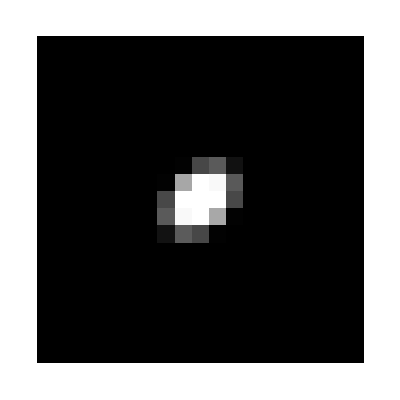

```mathematica
smp=bundle[voxPitch,30µLensPitch,45,45];
Print@@smp[[1]];Print["bounding box=",smp[[2]],", all distances in micron"];
Graphics3D[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"]]
tmp1=Ceiling[smp[[2,1]]/voxPitch/2];  (*take a vertical slice at x-position tmp1*)
Graphics[Raster[smp[[3,All,All,Dimensions[smp[[3]]][[3]]/2//Ceiling]]]]
```

#### Export and import simulated objects

```mathematica
SetDirectory["/Users/rudolfo/Desktop"]
```

/Users/rudolfo/Desktop

```mathematica
SetDirectory["/Users/rudolfo/People/Grant B. Harris/2020/Grant2020_08"]
```

/Users/rudolfo/People/Grant B. Harris/2020/Grant2020_08

```mathematica
Round[1.23456,0.001]
```

1.235

```mathematica
(*numerical values of the fluorescence density rounded to the 4th decimal*)
smp=bundle[voxPitch,15voxPitch,0,90];
Export["Bundle2_azim"<>ToString[smp[[1,-5]]]<>"_incl"<>ToString[smp[[1,-2]]]<>".txt",Append[Drop[smp,-1],Round[10000smp[[-1]]]/10000//N],"List"];
(*when using Round[tmp[[-1]],0.0001] instead of Round[10000 tmp[[-1]]]/10000//N, the numbers in the file can look like 0.11170000000000001 instead of 0.1117*)
```

```mathematica
smp=bundle[2voxPitch,30voxPitch,90,45];
```

```mathematica
smp[[1,4]]/voxPitch
```

2.5

```mathematica
Print["Bundle1_azim"<>ToString[smp[[1,-5]]]<>"_incl"<>ToString[smp[[1,-2]]]<>".txt"];
Graphics3D[{Translate[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"],(voxCtr+displace-smp[[1,2]])/voxPitch],
		boxSize=18;bounding={voxNrList/2-{boxSize,boxSize,boxSize},voxNrList/2+{boxSize,boxSize,boxSize}};
		PointSize[0.05],Point[bounding[[1]]]},
	PlotRange->Transpose[bounding],
	Axes->True,Ticks->None,AxesLabel->{X,Y,Z}(*,ViewPoint->{0,-Infinity,0}*)]
```

Bundle1_azim90_incl45.txt

-Graphics3D-

```mathematica
|
```

Importing a text file that contains a list and was previously exported using Export[ “... .txt”, anyList]

```mathematica
(*ToExpression[]converts a String that looks like an array into a Mathematica array*)
tmp=ToExpression/@Import["GUV2Test.txt","List"];
```

```mathematica
Dimensions[tmp]
```

{3}

```mathematica
tmp[[1]]
```

{GUV center=,{32.005,32.005,32.005},, GUV radius=,30.275,, membrane thick=,1.73,, voxPitch=,1.73}

```mathematica
tmp[[1]]//InputForm
(*When writing straight output of tmp[[1]], the distinction between String text and numbers is not apparent. When writing it in InputForm, it does become apparent*)
```

{"GUV center=", {32.005, 32.005, 32.005}, ", GUV radius=", 30.275, ", membrane thick=", 1.73, ", voxPitch=", 1.73}

```mathematica
Print@@tmp[[1]]
```

GUV center={32.005,32.005,32.005}, GUV radius=30.275, membrane thick=1.73, voxPitch=1.73

```mathematica
Dimensions[tmp[[3]]]
```

{37,37,37}

```mathematica
tmp[[3,19,19,2]]
```

0.9571

```mathematica
(*end*)
```

### Ray trace graphics

```mathematica
voxCtr/voxPitch
```

{11/2,29/2,29/2}

#### Playground

```mathematica
rayEnter[[2]]
```

{0.,314.871,156.195}

```mathematica
smp=guvOnGlass[50,voxPitch];
```

```mathematica
displace
```

```mathematica
(*rayNr=17;*)
displace={0voxPitch,0voxPitch,0voxPitch};(*displacement from voxCtr*)
Graphics3D[{
	Opacity[0.05],
	Raster3D[smp[[3]],{voxCtr-smp[[2]]/2+displace,voxCtr+smp[[2]]/2+displace}],
	Opacity[0.2],
	Magenta,
	objectCubeGraphics,
	Blue,Opacity[0.02],
	EdgeForm[],Cylinder[{{0,voxCtr[[2]],voxCtr[[3]]},{0.1,voxCtr[[2]],voxCtr[[3]]}},voxCtr[[1]]Tan[ArcSin[naObj/nMedium]]],
	Opacity[1],Green,
	entranceFaceGraphics,
	exitFaceGraphics,
	Opacity[1],Blue,Thick,
	Arrow[{rayEnter[[rayNr]],rayExit[[rayNr]]}] ,
	Red,PointSize[0.04],Point[rayEnter[[rayNr]]+0.3453(rayExit[[rayNr]]-rayEnter[[rayNr]])]
},Axes->True,AxesLabel->{X,Y,Z}(*,ViewPoint->{0,0,Infinity}*)]
```

```mathematica
smp[[1;;3]]
```

{{GUV center=,{53.375,53.375,53.375},, GUV radius=,51.625,, membrane thick=,1.75},{106.75,106.75,106.75},{61,61,61}}

```mathematica
guvOnGlass[50,voxPitch][[2]]
```

{32,61,61}

```mathematica
Image3D[smp[[3]]]
```

-Graphics3D-

```mathematica
(voxCtr[[1]]+displace[[1]]-(smp[[2,1]]-smp[[1,2,1]]))/voxPitch
```

0.

```mathematica
voxNrListTest
```

{{2,4},{0,15},{0,15}}

```mathematica
(*test-siddon*)
rayNr=17;
voxNrListTest={{0,5},voxNrYZ,voxNrYZ};
rT=rayTrace[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxNrListTest]
mP=midPoints[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxNrListTest]
iL=intersectLength[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxNrListTest]
```

{0.,0.0410543,0.095178,0.172182,0.2,0.257107,0.303309,0.4,0.419036,0.434436,0.565564,0.580964,0.6,0.696691,0.742893,0.8,0.827818,0.904822,0.958946,1.}

{{5.13178,192.173,226.949},{17.029,210.319,241.644},{33.42,235.319,261.888},{46.5227,255.304,278.072},{57.1384,271.495,291.183},{70.052,291.191,307.133},{87.9136,318.435,329.194},{102.379,340.498,347.061},{106.684,347.064,352.378},{125.,375.,375.},{143.316,402.936,397.622},{147.621,409.502,402.939},{162.086,431.565,420.806},{179.948,458.809,442.867},{192.862,478.505,458.817},{203.477,494.696,471.928},{216.58,514.681,488.112},{232.971,539.681,508.356},{244.868,557.827,523.051}}

{22.6075,29.8044,42.4038,15.3188,31.4471,25.4423,53.2451,10.4824,8.48075,72.2082,8.48075,10.4824,53.2451,25.4423,31.4471,15.3188,42.4038,29.8044,22.6075}

```mathematica
(*test-siddon*)
rayNr=22;
voxNrListTest={{0,5},voxNrYZ,voxNrYZ};
rT=rayTrace[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxNrListTest]
mP=midPoints[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxNrListTest]
iL=intersectLength[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxNrListTest]
```

{0.,0.0691956,0.2,0.356399,0.4,0.6,0.643601,0.8,0.930804,1.}

{{8.64945,366.484,293.977},{33.6495,368.314,311.386},{69.5498,370.942,336.386},{94.5498,372.771,353.795},{125.,375.,375.},{155.45,377.229,396.205},{180.45,379.058,413.614},{216.351,381.686,438.614},{241.351,383.516,456.023}}

{21.1181,39.9207,47.7318,13.3069,61.0387,13.3069,47.7318,39.9207,21.1181}

```mathematica
Length[rT]
Length[mP]
Length[iL]
```

20

19

19

```mathematica
smp[[2,1]]+smp[[1,2,1]]-voxCtr[[1]]
```

250

```mathematica
voxNrListTest={{voxCtr[[1]]-(smp[[2,1]]-smp[[1,2,1]]),voxCtr[[1]]+(smp[[2,1]]-smp[[1,2,1]])}/voxPitch,voxNrYZ,voxNrYZ}
```

{{2,9},29,29}

```mathematica
voxCtr
```

{275/2,725/2,725/2}

```mathematica
smp[[1]]
```

{{GUV center=,{53.375,53.375,53.375},, GUV radius=,51.625,, membrane thick=,1.75},{106.75,106.75,106.75},{1}}
 |  |  |  |

```mathematica
voxNrList
```

{11,29,29}

```mathematica
smp=guvOnGlass[50,voxPitch];
```

```mathematica
Dimensions[Drop[smp[[3]],0,0,10]]
```

{61,61,51}

```mathematica
Image3D[Drop[guvOnGlass[50,voxPitch][[3]],0,0,10]]
```

-Graphics3D-

```mathematica
Image3D[Drop[guvOnGlass[50,voxPitch][[3]],10]]
```

-Graphics3D-

```mathematica
rayNr=41;
smp=guv[17µLensPitch,voxPitch];
displace={0voxPitch,0voxPitch,0voxPitch};(*displacement from voxCtr*)
voxBoxNrs=Transpose[{voxCtr+displace-smp[[2]]/2,voxCtr+displace+smp[[2]]/2}]/voxPitch//Round
Length[rT=rayTrace[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxBoxNrs]]
Length[mP=midPoints[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxBoxNrs]]
Length[iL=intersectLength[rayEnter[[rayNr]],rayExit[[rayNr]],voxPitchList,voxBoxNrs]]
Graphics3D[{
	Opacity[0.01],
	Raster3D[smp[[3]],{voxCtr-smp[[2]]/2+displace,voxCtr+smp[[2]]/2+displace}(*,ColorFunction->"GrayLevelOpacity"*)],
	Blue,Opacity[0.02],
	EdgeForm[],Cylinder[{{0,voxPitch*voxNrYZ/2,voxPitch*voxNrYZ/2},{0.1,voxPitch*voxNrYZ/2,voxPitch*voxNrYZ/2}},256],
	Opacity[1],Green,
	entranceFaceGraphics,
	exitFaceGraphics,
	Opacity[1],Blue,Thick,
	Line[{rayEnter[[rayNr]],rayExit[[rayNr]]}],
	PointSize[Large]
(*	Point[mP],
	Red,Point[Table[rayEnter[[rayNr]]+rT[[i]](rayExit[[rayNr]]-rayEnter[[rayNr]]),{i,Length[rT]}]]*)
},Axes->True,AxesLabel->{"x","y","z"},ViewPoint->{0,0,Infinity},ImageSize->200]
```

{{54,91},{184,221},{184,221}}

56

55

55

-Graphics3D-

```mathematica
smp[[3]][[2,tmp=1+smp[[2,3]]/2/voxPitch//Round,tmp]]
```

0.876383

```mathematica
Dimensions[smp[[3]]]
```

{7,7,7}

### Generating light field images

#### Code explanation

The following explanation of the code for generating light field images is taken from my email to Grant Harris on May 7, 2020:

The code 
mP = Plus[#, {0, jj µLensPitch, kk µLensPitch}] & /@ mP0[[ii]]
uses some short forms and can also be written as
mP = Map[Function[Plus[#, {0, jj µLensPitch, kk µLensPitch}],mP0[[ii]]]

This might not help much, so here is a narrative explanation:
mP0 is the list of midpoint coordinates for all 164 rays. Hence, mP0 is a list of lists, where the ii index enumerates the rays from 1 to Length[rayEnterCamPix]=164. Each mP0[[ii]] is itself a list of voxel midpoints that the ray ii traverses. The midpoints are given by their {x, y, z} coordinates. (The midpoints are not the voxel centers, but the midpoints of the intersection lengths along the ray path; see Siddon paper). 

Since mP0 is the list of lists for the central microlens only, when calculating the pattern behind a microlens that is displaced by jj and kk times the µLensPitch from the object space center, we need to add the displacement vector {0, jj µLensPitch, kk µLensPitch} to each coordinate in the mP0[[ii]] list before using the coordinate list, now called mP, to identify the object voxels that a ray of a displaced µLens traverses.

You can find definitions of the Map[], Function[], and Plus[] operators online by googling “mathematica map”, for example. With these explanations, see if you can transfer the above operation into Python.

The code tmp2 = Ceiling[Transpose[Reverse[Transpose[mP]]]/voxPitch]
converts the midpoint coordinates into integers, using Ceiling. The integer coordinates identify the object voxels that are traversed by ray ii. Reverse and Transpose put the converted midpoints into the column and row order required to match the convention used for identifying object voxels.

The code camArray[[rayEnterCamPix[[ii, 1]], rayEnterCamPix[[ii, 2]]]] = Plus @@ (Extract[smpArray, tmp2] Reverse[iL[[ii]]])
is the last assignment in the Do loop, which ends with {ii, Length[rayEnterCamPix]}.

camArray is the list of intensity values that are assigned to the 16 by 16 pixels behind a µLens. 
Plus @@ (Extract[smpArray, tmp2] Reverse[iL[[ii]]]) can also be written as Apply[Plus, Extract[smpArray, tmp2] Reverse[iL[[ii]]]] and does the following:
Extract[smpArray, tmp2] extracts the fluorescence intensity values associated with the object voxels that are identified by tmp2. After the extraction, the intensity values are in the form of a list which is then multiplied by the list of intersection lengths iL[[ii]] for ray ii. The multiplication of two lists of equal length occurs element by element and creates a list of products. It might be good to realize here, that while the midpoint coordinates mP change for each microlens identified by jj and kk, the intersection length values do not change with the translocation. Finally, the list of products is added up by applying the Plus operator to the list to generate the intensity value recorded in the camera pixel associated with ray ii.

The final expression Image[camArray/100, ImageSize -> 32
converts the array of intensity values into an image that represents the intensity values in the 16 by 16 pixels behind a microlens.

The lfImageArray is the list of images that represent each microlens in the raster defined by jj and kk.

#### Code for generating light field images

```mathematica
(*Comment out Image3D[smpArray] and Show[%,... for voxPitch smaller than 1.75µm*)
smp=bundle[voxPitch,15µLensPitch,0,90];jjkkMinMax=Round[{-16,16,-16,16}];(*number of microlenses in y- and z-direction; the larger the object the more microlenses*)
displace={0µLensPitch,0voxPitch,0voxPitch};(*displacement from voxCtr*)
Print@@smp[[1]];
subµLns=Floor[µLensPitch/(2voxPitch)];
(*thisRayEnter and thisRayExit are ray enter and exit coordinates translated to the front and back plane, respectively, where the sample starts and ends along the x-direction*)
thisRayEnter=Table[tmp=rayEnter[[i]]+(voxCtr[[1]]+(-smp[[2,1]]/2+displace[[1]]))/voxCtr[[1]](voxCtr-rayEnter[[i]]);{0,tmp[[2]],tmp[[3]]},{i,nrRays}];
(*Print["rayEnter = ",rayEnter];
Print["thisRayEnter = ",thisRayEnter];*)
thisRayExit=Table[tmp=rayEnter[[i]]+(voxCtr[[1]]+(smp[[2,1]]/2+displace[[1]]))/voxCtr[[1]](voxCtr-rayEnter[[i]]);{smp[[2,1]],tmp[[2]],tmp[[3]]},{i,nrRays}];
(*Print["thisRayExit = ",thisRayExit];*)
(*smpBoxNrs0 is the space centered on voxCtr that includes the index depth of the sample along X and the Y and Z voxPitch index ranges that include all µLenses with rays that interact with the sample*)
smpBoxNrs0=Transpose[{{0,voxCtr[[2]]-smp[[2,2]]/2,voxCtr[[3]]-smp[[2,3]]/2},{smp[[2,1]],voxCtr[[2]]+smp[[2,2]]/2,voxCtr[[3]]+smp[[2,3]]/2}}+(Abs[displace[[1]]]+smp[[2,1]]/2){{0,-Tan[ArcSin[naObj/nMedium]],-Tan[ArcSin[naObj/nMedium]]},{0,Tan[ArcSin[naObj/nMedium]],Tan[ArcSin[naObj/nMedium]]}}]/voxPitch//Round;
Print["smpBoxNrs0 = ",smpBoxNrs0];
(*smpBoxNrs identifies the space in index numbers that has the sample object inside*)
(*For smpBoxNrs and sampBoxNrs0, the X-index is 0 where the object starts and extends in X to the end of the object*)
smpBoxNrs=Transpose[{tmp1=voxCtr+displace-smp[[2]]/2;{0,tmp1[[2]],tmp1[[3]]},tmp2=voxCtr+displace+smp[[2]]/2;{smp[[2,1]],tmp2[[2]],tmp2[[3]]}}]/voxPitch//Round;
Print["smpBoxNrs = ",smpBoxNrs];
(*smpBoxNrsPrint shows in global indices the box coordinates that contains the object, including its displacement if any*)
smpBoxNrsPrint=Transpose[{voxCtr+displace-smp[[2]]/2,voxCtr+displace+smp[[2]]/2}]/voxPitch//Round;
Print["sample box = ",smpBoxNrsPrint, " [numbers]"];
objectArray=ArrayPad[smp[[3]],Transpose[(Transpose[Reverse[smpBoxNrs]]-{{0,0,0},{voxNrYZ,voxNrYZ,smp[[2,1]]/voxPitch//Round}}){1,-1}]];
Graphics3D[{Translate[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"],(voxCtr+displace-smp[[1,2]])/voxPitch],Blue,Line[{rayEnter[[186]],rayExit[[186]]}/voxPitch],Line[{rayEnter[[147]],rayExit[[147]]}/voxPitch],Line[{rayEnter[[41]],rayExit[[41]]}/voxPitch],Line[{rayEnter[[2]],rayExit[[2]]}/voxPitch]},PlotRange->{{0,voxNrX},{0,voxNrYZ},{0,voxNrYZ}},ViewPoint->{0,-Infinity,0}]
rayEnterCamPix=Table[camRayEntrance[[i,1]],{i,nrRays}]; (*List of {i,j} coordinates of camera pixels that correspond to rays that enter object space*)
mP0=Table[midPoints[thisRayEnter[[i]],thisRayExit[[i]],voxPitchList,smpBoxNrs0],{i,nrRays}];(*list of midPoint lists for every ray within naObj centered on voxCtr*)
iL=Table[intersectLength[thisRayEnter[[i]],thisRayExit[[i]],voxPitchList,smpBoxNrs0],{i,nrRays}];(*list of intersectLength lists for every ray within naObj centered on voxCtr; this list remains the same even when the µLens is shifted in y- and z-direction*)
Timing[Monitor[
	camArray=Table[0,{i,nrCamPix},{j,nrCamPix}];
	lfImageArray=Table[
		Do[mP0ii=Plus[#,{0,jj µLensPitch,kk µLensPitch}]&/@mP0[[ii]]; (*moving the midPoints by increments of µLensPitch*)
			camArray[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0;
			Do[mP=Plus[#,{0,jjj voxPitch,kkk voxPitch}]&/@mP0ii; (*moving the midPoints by increments of voxPitch within a µLensPitch*)
					tmp2=Ceiling[Reverse[mP,2]/voxPitch];  (*Reverse[mP,2] puts the part identifier in the right order [[k,j,i]]*)
					tmp3=Extract[objectArray,tmp2];
(*					camArray[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Plus@@(tmp3×iL[[ii]]),*)
					camArray[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Sum[tmp3[[i]]×iL[[ii,i]],{i,Length[iL[[ii]]]}],
			{jjj,-subµLns,subµLns},{kkk,-subµLns,subµLns}],
		{ii,nrRays}];
		Image[camArray,ImageSize->32],
	{jj,jjkkMinMax[[1]],jjkkMinMax[[2]]},{kk,jjkkMinMax[[3]],jjkkMinMax[[4]]}];,
{"row = ",jj}]]
```

Bundle center {X,Y,Z}={13.,2.6,2.6}, radius=2.6, length=26.8667, voxPitch=1.73333, rotation azim=0°, rotation incl=90°

smpBoxNrs0 = {{0,15},{185,220},{185,220}}

smpBoxNrs = {{0,15},{201,204},{201,204}}

sample box = {{65,80},{201,204},{201,204}} [numbers]

-Graphics3D-

{42.9946,Null}

```mathematica
lfImageIso=ImageAssemble[Transpose[100lfImageArray]];
ImageDimensions[%]
lfImageIso//ImageAdjust
```

{528,528}

-Graphics-

```mathematica
ImageDimensions[%]
```

{784,784}

```mathematica
%/16
```

{37,37}

```mathematica
Max[ImageData[lfImageIso]]
```

4224.99

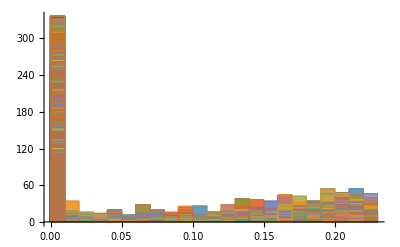

```mathematica
Histogram[ImageData[lfImage]]
```

```mathematica
voxPitch
```

1.73333

```mathematica
SetDirectory["/Users/rudolfo/Desktop"]
```

/Users/rudolfo/Desktop

```mathematica
Export["Bundle2_azim0_incl90_LF33uLens_rNA7.7.tif",lfImageIso//ImageAdjust]
```

Bundle2_azim0_incl90_LF33uLens_rNA7.7.tif

```mathematica
i1=ImageAssemble[Transpose[Drop[lfImageArray,0,1]]];
i2=ImageReflect[ImageAssemble[Transpose[Drop[lfImageArray,1,0]]],Left];
i3=ImageReflect[ImageAssemble[Transpose[Drop[lfImageArray,1,1]]],Left];
i4=ImageAssemble[{{ImageReflect[i1]},{lfImage}}];
i5=ImageAssemble[{{ImageReflect[i3]},{i2}}];
ImageAssemble[{i5,i4}]//ImageAdjust
```

-Graphics-

```mathematica
ImageDimensions[%]
```

{976,976}

```mathematica
Export["image.tiff",%167]
```

image.tiff

```mathematica
SetDirectory["/Users/rudolfo/LightFieldMicroscopy/Simulations/2019/"];
```

```mathematica
(*end*)
```

## Anisotropic Fluorescence

### Dipole radiation pattern

```mathematica
(*Formula for the amplitude of the far field of radiation going off in different directions represented by spherical coordinates u and v*)
(*Dipole moment is assumed to have length 1 and is parallel to x-axis, *)
(*u is angle between direction and dipole moment, v is angle between y-axis and the projection of the direction into y-z plane*)
(*Amplitude is projection of the dipole moment into the plane perpendicular to direction (direction is normal to that plane)*) 
(*The amplitude can be represented as the surface of a torus*)
fieldAmp[u_,v_]:={Sin[u]Cos[u],Sin[u]^2Cos[v],Sin[u]^2Sin[v]}

ray[u_,v_]:={Cos[u],Sin[u]Cos[v],Sin[u]Sin[v]}

(*The field amplitude can also be expressed as the Cross product between the orientation of the dipole moment and the direction of the ray carrying the emitted field*)
fieldAmpSqr[u_,v_]:=Power[Norm[{1,0,0}×ray[u,v]],2]*ray[u,v]

(*The field component passed by a polarizer that is perpendicular to the ray direction coming from a dipole
  is equal to the dot product of the polarizer direction and the dipole direction*)

(*discretized field amplitude*)
angleStep=Pi/32;
fieldAmpDiscr=Table[fieldAmp[u,v],{u,0,Pi,angleStep},{v,0,2Pi,angleStep}];
```

```mathematica
ParametricPlot3D[fieldAmp[u,v],{u,0,Pi},{v,0,2Pi},BoundaryStyle->Black,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[fieldAmpSqr[u,v],{u,0,Pi},{v,0,2Pi},BoundaryStyle->Black,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[fieldAmpDiscr,AxesLabel->{x,y,z},BoxRatios->{1,2,2}]
```

-Graphics3D-

### Simulated objects with embedded dipole emitters, all locations and distances in micron

#### Ball, ball[radius,theta,azim,ratio,dip], is a solid ball with one or more dipole emitters. The ball’s radius is made to be an odd number of voxPitch, including one, with its center in the center of a voxel (e.g. radius=0 will result in a ball radius of 0.5 voxPitch). For dip=0, the fluorophores are considered monopole emitters. For dip≠0, the ball is filled with three dipoles per voxel. The first dipole represents the symmetry axis whose orientation is defined by angles azim and theta. For azim=theta=0, the first dipole is oriented parallel to the x-axis. All dipoles are rotated around the y-axis by the angle theta [deg] away from the x-axis, and then rotated by azim around the x-axis. The first dipole of three per voxel represents the symmetry axis of a uniaxial distribution at a given voxel and its length is equal to one. For dip=1, the other two vectors are always {0,0,0}, independent of ratio. For dip=2, the two other vectors have equal length of 1/ratio. If the ratio is smaller than 1, then the other two vectors have length one, and the vector parallel to the symmetry axis has length ratio. The orientations of the three dipoles per voxel are the same in every voxel of the ball.

```mathematica
ball[radius_,theta_,azim_,ratio_,dip_]:=
Module[{r,rotAzim,rotTheta,smpRegion,smpBounds,rSize,smpArray,x,y,z,dipVec,ratioVec,dipArray},
r=(Round[radius/voxPitch]+0.5)voxPitch; (*the 0.5 puts the center of the ball in the center of a voxel*)
rotTheta=RotationMatrix[theta Degree,{0,1,0}];
rotAzim=RotationMatrix[azim Degree,{1,0,0}];
dipVec=rotAzim.(rotTheta.{1,0,0});
smpRegion=Region@Ball[{0,0,0},r];
smpBounds=RegionBounds[smpRegion];
rSize=Round[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])/voxPitch];Do[If[EvenQ[rSize[[i]]],rSize[[i]]+=1],{i,3}];
smpArray=Clip[Reverse[ImageData[RegionImage[smpRegion,RegionBounds[smpRegion],RasterSize->rSize]],{1,2}],{0,Infinity}];
If[dip==1,dipArray=Table[If[smpArray[[k,j,i]]>0,{dipVec,{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}],Null];
If[dip==2,If[ratio⩾1,ratioVec={1,1/ratio,1/ratio},ratioVec={ratio,1,1}];dipArray=Table[If[smpArray[[k,j,i]]>0,{x,y,z}=dipVec;ratioVec Orthogonalize[{{x,y,z},If[y==0&&z==0,{0,1,0},{0,-z,y}],If[y==0&&z==0,{0,0,1},Cross[{x,y,z},{0,-z,y}]]}],{{0,0,0},{0,0,0},{0,0,0}}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}],Null];
{{"Ball center {X,Y,Z}=",rSize voxPitch/2,", radius=",r,", voxPitch=",voxPitch,", rotation theta=",theta,"°",", rotation azim=",azim,"°"," , ratio=",ratio,", dipole flag=",dip},rSize voxPitch,smpArray,dipArray}]
```

Graphics

Ball center {X,Y,Z}={2.595,2.595,2.595}, radius=2.01833, voxPitch=0.576667, rotation theta=90°, rotation azim=45° , ratio=0.5, dipole flag=1

bounding box={5.19,5.19,5.19}, distances in micron

-Graphics3D-

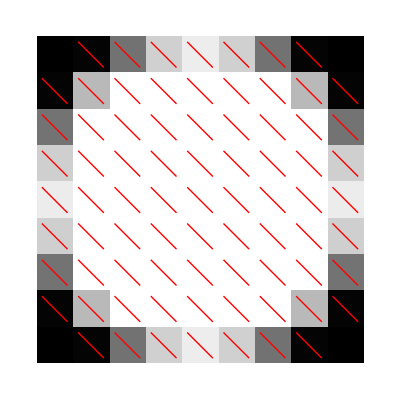

-Graphics3D-

```mathematica
smp=ball[µLensPitch,90,45,0.5,1];
Print@@smp[[1]];Print["bounding box=",smp[[2]],", distances in micron"];
Graphics3D[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"]]
tmp1=Ceiling[smp[[2,1]]/voxPitch/2];  (*take a vertical slice at x-position tmp1*)
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{j-0.5,k-0.5}-Drop[smp[[4,k,j,tmp1,1]],1]/2,{j-0.5,k-0.5}+Drop[smp[[4,k,j,tmp1,1]],1]/2},
			{j,smp[[2,2]]/voxPitch//Round},{k,smp[[2,3]]/voxPitch//Round}],1],Null];
Graphics[{Raster[smp[[3,All,All,Dimensions[smp[[3]]][[3]]/2//Ceiling]]],If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]}]
If[smp[[1,-1]]≠0,
	tmp2=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[4,k,j,i,1]]/2,{i-0.5,j-0.5,k-0.5}+smp[[4,k,j,i,1]]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],2],Null];
	Graphics3D[{Red,Map[Line,tmp2]},ImageSize->200]]
```

#### GUV (Giant Unilamellar Vesicle), guv[guvRadius,membraneThickness,ratio,dip] is a Giant Unilamellar Vesicle. For dip≠0, the patch has three vectors in each voxel that is part of the membrane. The first one points to the center of the GUV and represents the symmetry axis of a uniaxial distribution at a given voxel and its length is equal to one. For dip=1, the other two vectors are always {0,0,0}, independent of ratio. For dip=2, the two other vectors have equal length of 1/ratio. If the ratio is smaller than 1, then the other two vectors have length one, and the vector parallel to the symmetry axis has length ratio.

```mathematica
(*Giant Unilamellar Vesicle (GUV) in object space, guvRadius (outer radius) and membraneThickness in micron*)
(*The dip flag is zero (dip=0) for random emitters in membrane; dip=1 for one or more fluorophores per voxel, each with its dipole axis normal to the membrane, {dipX,dipY,dipZ} is a unit vector in the direction either away from or towards the GUV center*)
(*dip=2 for three directions of fluorophores per voxel, one normal to the membrane, {dipX,dipY,dipZ} is a unit vector in the direction either away from or towards the GUV center, and {dip1X,dip1Y,dip1Z} and {dip2X,dip2Y,dip2Z} tangential to the membrane and orthogonal to each other*)
(*ratio is the ratio of the number of fluorophores along {dipX,dipY,dipZ} over the number of fluorophores along {dip1X,dip1Y,dip1Z} and {dip2X,dip2Y,dip2Z}, where the number of fluorophores along {dip1X,dip1Y,dip1Z} and {dip2X,dip2Y,dip2Z} is equal when simulating a uniaxial distribution*)
(*placed in sample space discretized by voxPitch; the center of the GUV is in the center of its own 3D voxel array*)
(*One corner of the bounding Box is at {0,0,0} and the diagonal corner is at {2gR,2gR,2gR}+2voxPitch*)
(*guv[guvRadius,membraneThickness,dip]={{"GUV center=",boundBoxMax/2,", GUV radius=",gR,", membrane thick=",mT},boundBoxMax,{3D array of voxel values}}*)
(*When dip=0, a single voxel value is a scalar that is proportional to the density of randomly oriented fluorophores*)
(*When dip=1, a single voxel value is a scalar and a unit vector specifying the dipole orientation, which is in the direction away from or towards the GUV center. The scalar is proportional to the density of aligned fluorophores*)
guv[guvRadius_,membraneThickness_,ratio_,dip_]:=
Module[{gC,gR,mT,i1,i2,i12Array,boundBoxMax,voxNr,tmp,ratioVec,x,y,z,dipVec},
gR=(Round[guvRadius/voxPitch]+0.5)voxPitch;  (*ensures that gR reaches the edge of a voxel in x,y,z directions*)
mT=Round[membraneThickness/voxPitch]voxPitch;
boundBoxMax=If[OddQ[tmp=Ceiling[2gR/voxPitch]],(tmp+2)voxPitch{1,1,1},(tmp+1)voxPitch{1,1,1}];
gC=boundBoxMax/2;
i1=RegionImage[Ball[gC,gR],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i2=RegionImage[Ball[gC,gR-mT],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i12Array=Reverse[ImageData[ImageSubtract[i1,i2]//ImageClip],{1,2}];
If[dip==0,dipVec=Null];
If[dip==1,dipVec=Table[If[i12Array[[k,j,i]]==0,{{0,0,0},{0,0,0},{0,0,0}},{Normalize[{i-0.5,j-0.5,k-0.5}voxPitch-boundBoxMax/2],{0,0,0},{0,0,0}}],{k,boundBoxMax[[3]]/voxPitch//Round},{j,boundBoxMax[[2]]/voxPitch//Round},{i,boundBoxMax[[1]]/voxPitch//Round}],Null];
If[dip==2,If[ratio⩾1,ratioVec={1,1/ratio,1/ratio},ratioVec={ratio,1,1}];dipVec=Table[If[i12Array[[k,j,i]]==0,{{0,0,0},{0,0,0},{0,0,0}},{x,y,z}=Normalize[{i-0.5,j-0.5,k-0.5}voxPitch-boundBoxMax/2];ratioVec Orthogonalize[{{x,y,z},If[y==0&&z==0,{0,1,0},{0,-z,y}],If[y==0&&z==0,{0,0,1},Cross[{x,y,z},{0,-z,y}]]}]],{k,boundBoxMax[[3]]/voxPitch//Round},{j,boundBoxMax[[2]]/voxPitch//Round},{i,boundBoxMax[[1]]/voxPitch//Round}],Null];
{{"GUV center {X,Y,Z}=",boundBoxMax/2,", GUV radius=",gR,", membrane thick=",mT,", voxPitch=",voxPitch,", ratio=",ratio,", dipole flag=",dip},boundBoxMax,i12Array,dipVec}]
```

Graphics

voxPitch = 0.577778
GUV center {X,Y,Z}={9.53333,9.53333,9.53333}, GUV radius=8.95556, membrane thick=0.577778, voxPitch=0.577778, ratio=5, dipole flag=1, boundBoxMax={19.0667,19.0667,19.0667}

-Graphics3D-

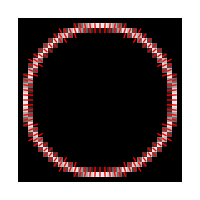

-Graphics3D-

```mathematica
smp=guv[5µLensPitch,voxPitch,5,1];
Print["voxPitch = ",voxPitch,"\n",smp[[1,1]],smp[[1,2]],smp[[1,3]],smp[[1,4]],smp[[1,5]],smp[[1,6]],smp[[1,7]],smp[[1,8]],smp[[1,9]],smp[[1,10]],smp[[1,11]],smp[[1,12]],", boundBoxMax=",smp[[2]]];
tmpI=Image3D[Reverse[smp[[3]],{1,2}]]
tmp1=Ceiling[smp[[2,3]]/voxPitch/2];  (*take a horizontal slice at z-position tmp1*)
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{i-0.5,j-0.5}-Drop[smp[[4,tmp1,j,i,1]],-1]/2,{i-0.5,j-0.5}+Drop[smp[[4,tmp1,j,i,1]],-1]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch}],1],Null];
Graphics[{Raster[ImageData[tmpI][[tmp1]]],If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]},ImageSize->200]
If[smp[[1,-1]]≠0,
	tmp2=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[4,k,j,i,1]]/2,{i-0.5,j-0.5,k-0.5}+smp[[4,k,j,i,1]]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],2],Null];
	Graphics3D[{Red,Map[Line,tmp2]},ImageSize->200]]
```

#### Membrane patch, membranePatch[radius,membraneThickness,azim,theta,ratio,dip], radius and thickness of the membrane (cylinder), azimuth (azim) and inclination angle (theta) of the membrane normal. For dip≠0, the patch has three vectors per voxel. The first one is normal to the membrane plane and represents the symmetry axis of a uniaxial distribution at a given voxel and its length is equal to one. For dip=1, the other two vectors are always {0,0,0}, independent of ratio. For dip=2, the two other vectors have equal length of 1/ratio. If the ratio is smaller than 1, then the other two vectors have length one, and the vector parallel to the symmetry axis has length ratio.

#### Notes

When dip=0, a single voxel value is a scalar that is proportional to the density of randomly oriented fluorophores
When dip=1, the first 3D array (membranePatch[[3]]) is an array of scalars and the second 3D array (membranePatch[[4]]) is an array of unit vectors specifying the dipole orientations, which are in the direction normal to the membrane. The scalar is proportional to the density of aligned fluorophores
Disk-shaped membrane patch, sitting on a glass surface, for example
The normal of the patch can be rotated around the y-axis by an angle theta [deg] away from the x-axis, and then rotated by azim around the x-axis. For theta = azim = 0, the patch lies in the y-z plane, with its normal parallel to x-axis.

```mathematica
membranePatch[radius_,thick_,theta_,azim_,ratio_,dip_]:=
Module[{r,t,normal,rotAzim,rotTheta,smpRegion,smpBounds,rSize,smpArray,x,y,z,ratioVec,dipArray},
r=(Round[radius/voxPitch]+0.5)voxPitch; (*the 0.5 puts the center of the bundle in the center of a voxel*)
t=Ceiling[thick/voxPitch];
If[EvenQ[t],t=(t+1)voxPitch,t=t voxPitch];
rotTheta=RotationMatrix[theta Degree,{0,1,0}];
rotAzim=RotationMatrix[azim Degree,{1,0,0}];
normal={rotAzim.(rotTheta.{-t/2,0,0}),rotAzim.(rotTheta.{t/2,0,0})};
smpRegion=Region@Cylinder[normal,r];
smpBounds=RegionBounds[smpRegion];
rSize=Round[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])/voxPitch];Do[If[EvenQ[rSize[[i]]],rSize[[i]]+=1],{i,3}];
smpArray=Clip[Reverse[ImageData[RegionImage[smpRegion,RegionBounds[smpRegion],RasterSize->rSize]],{1,2}],{0,Infinity}];
If[dip==1,normal=Normalize[normal[[2]]];dipArray=Table[If[smpArray[[k,j,i]]>0,{normal,{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}]];
If[dip==2,If[ratio⩾1,ratioVec={1,1/ratio,1/ratio},ratioVec={ratio,1,1}];normal=Normalize[normal[[2]]];dipArray=Table[If[smpArray[[k,j,i]]>0,{x,y,z}=normal;ratioVec Orthogonalize[{{x,y,z},If[y==0&&z==0,{0,1,0},{0,-z,y}],If[y==0&&z==0,{0,0,1},Cross[{x,y,z},{0,-z,y}]]}],{{0,0,0},{0,0,0},{0,0,0}}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}],Null];
{{"Patch center {X,Y,Z}=",rSize voxPitch/2,", radius=",r,", membrane thickness=",t,", voxPitch=",voxPitch,", rotation azim=",azim,"°",", rotation theta=",theta,"°"," , ratio=",ratio,", dipole flag=",dip},rSize voxPitch,smpArray,dipArray}]
```

Graphics

Patch center {X,Y,Z}={3.74833,4.61333,4.61333}, radius=4.90167, membrane thickness=0.576667, voxPitch=0.576667, rotation azim=45°, rotation theta=45° , ratio=0.5, dipole flag=2

bounding box={7.49667,9.22667,9.22667}, distances in micron

-Graphics3D-

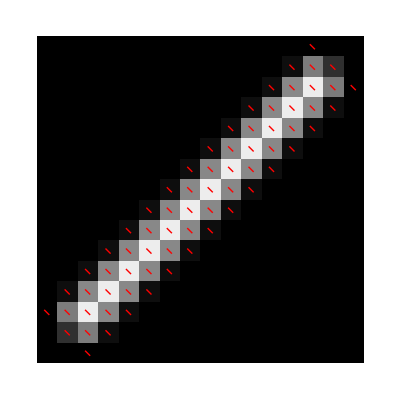

-Graphics3D-

```mathematica
smp=membranePatch[8voxPitch,1voxPitch,45,45,0.5,2];
Print@@smp[[1]];Print["bounding box=",smp[[2]],", distances in micron"];
Graphics3D[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"]]
tmp1=Ceiling[smp[[2,1]]/voxPitch/2];  (*take a vertical slice at x-position tmp1*)
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{j-0.5,k-0.5}-Drop[smp[[4,k,j,tmp1,1]],1]/2,{j-0.5,k-0.5}+Drop[smp[[4,k,j,tmp1,1]],1]/2},
			{j,smp[[2,2]]/voxPitch//Round},{k,smp[[2,3]]/voxPitch//Round}],1]];
Graphics[{Raster[smp[[3,All,All,Dimensions[smp[[3]]][[3]]/2//Ceiling]]],If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]}]
If[smp[[1,-1]]≠0,tmp2=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[4,k,j,i,1]]/2,{i-0.5,j-0.5,k-0.5}+smp[[4,k,j,i,1]]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],2],Null];
	Graphics3D[{Red,Map[Line,tmp2]},ImageSize->200]]
```

#### Bundle, bundle[radius,length,azim,incl,ratio,dip], radius and length of the straight bundle (cylinder), azimuth (azim) and inclination angle (incl) of the bundle axis (azim and incl given in Degree). For dip≠0, the bundle has three vectors per voxel. The first one is parallel to the bundle axis and represents the symmetry axis of a uniaxial distribution at a given voxel and its length is equal to one. For dip=1, the other two vectors are always {0,0,0}, independent of ratio. For dip=2, the two other vectors have equal length of 1/ratio. If the ratio is smaller than 1, then the other two vectors have length one, and the vector parallel to the symmetry axis has length ratio.

#### Notes

The bundle can be rotated by azim [deg] around the x-axis and angle incl [deg] towards the x-axis. The angle incl is a rotation around the axis that is perpendicular to the x-axis and the new bundle axis after rotation by azim. For azim = incl = 0, the bundle lies parallel to the y-axis

```mathematica
bundle[radius_,length_,azim_,incl_,ratio_,dip_]:=
Module[{r,l,bAxis,rota,roti,smpRegion,smpBounds,rSize, smpArray,x,y,z,ratioVec,dipArray},
r=(Round[radius/voxPitch]+0.5)voxPitch; (*the 0.5 puts the center of the bundle in the center of a voxel*)
l=(Round[length/voxPitch]+0.5)voxPitch;
rota=RotationMatrix[azim Degree,{1,0,0}];
roti=RotationMatrix[incl Degree,rota.{0,0,1}];
bAxis={roti.(rota.{0,-l/2,0}),roti.(rota.{0,l/2,0})};
smpRegion=Region@Cylinder[bAxis,r];
smpBounds=RegionBounds[smpRegion];
rSize=Round[(Transpose[smpBounds][[2]]-Transpose[smpBounds][[1]])/voxPitch];Do[If[EvenQ[rSize[[i]]],rSize[[i]]+=1],{i,3}];
(*Print["rSize = ",rSize];*)
smpArray=Clip[Reverse[ImageData[RegionImage[smpRegion,smpBounds,RasterSize->rSize]],{1,2}],{0,Infinity}];
If[dip==1,bAxis=Normalize[bAxis[[2]]];dipArray=Table[If[smpArray[[k,j,i]]>0,{bAxis,{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}],Null];
If[dip==2,If[ratio⩾1,ratioVec={1,1/ratio,1/ratio},ratioVec={ratio,1,1}];bAxis=Normalize[bAxis[[2]]];dipArray=Table[If[smpArray[[k,j,i]]>0,{x,y,z}=bAxis;ratioVec Orthogonalize[{{x,y,z},If[y==0&&z==0,{0,1,0},{0,-z,y}],If[y==0&&z==0,{0,0,1},Cross[{x,y,z},{0,-z,y}]]}],{{0,0,0},{0,0,0},{0,0,0}}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}],Null];
{{"Bundle center {X,Y,Z}=",rSize voxPitch/2,", radius=",r,", length=",l,", voxPitch=",voxPitch,", rotation azim=",azim,"°",", rotation incl=",incl,"°"," , ratio=",ratio,", dipole flag=",dip},rSize voxPitch,smpArray,dipArray}]
```

Graphics

Bundle center {X,Y,Z}={26.3825,3.0275,3.0275}, radius=3.0275, length=52.3325, voxPitch=0.865, rotation azim=0°, rotation incl=90° , ratio=1, dipole flag=0

bounding box={52.765,6.055,6.055}, distances in micron

-Graphics3D-

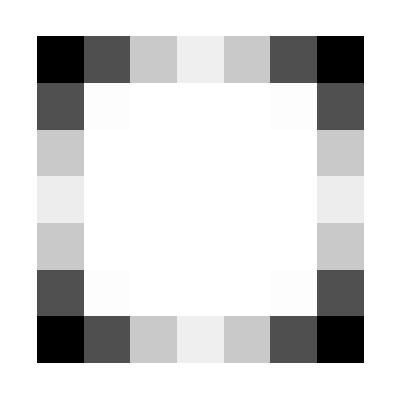

```mathematica
smp=bundle[3voxPitch,30µLensPitch,0,90,1,0];
Print@@smp[[1]];Print["bounding box=",smp[[2]],", distances in micron"];
Graphics3D[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"]]
tmp1=Ceiling[smp[[2,1]]/voxPitch/2];  (*take a vertical slice at x-position tmp1*)
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{j-0.5,k-0.5}-Drop[smp[[4,k,j,tmp1,1]],1]/2,{j-0.5,k-0.5}+Drop[smp[[4,k,j,tmp1,1]],1]/2},
			{j,smp[[2,2]]/voxPitch//Round},{k,smp[[2,3]]/voxPitch//Round}],1],Null];
Graphics[{Raster[smp[[3,All,All,Dimensions[smp[[3]]][[3]]/2//Ceiling]]],If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]}]
If[smp[[1,-1]]≠0,tmp2=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[4,k,j,i,1]]/2,{i-0.5,j-0.5,k-0.5}+smp[[4,k,j,i,1]]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],2],Null];
	Graphics3D[{Red,Map[Line,tmp2]},ImageSize->200]]
```

#### Using Manipulate for rotating bundle, etc.

```mathematica
Manipulate[smpMan=bundle[4voxPitch,4µLensPitch,i,j,1,0];pad=Floor[({17,17,17}-Dimensions[smp[[3]]])/2];object=ArrayPad[smpMan[[3]],pad];
			Graphics3D[{Thick,Arrowheads[0.1],Arrow[{{0,-1,-1},{17,-1,-1}}],Raster3D[object,ColorFunction->"GrayLevelOpacity"]},PlotRange->{{-2,18},{-2,18},{-2,18}}],{i,0,180,22.5},{j,0,157.5,22.5}]
```

Part::partd: Part specification smp⟦3⟧ is longer than depth of object.

Thread::tdlen: Objects of unequal length in {17,17,17}+{-2} cannot be combined.

Thread::tdlen: Objects of unequal length in {-2}+{17,17,17} cannot be combined.

ArrayPad::arr: First argument 0 to ArrayPad should be an array.

Part::partd: Part specification smp⟦3⟧ is longer than depth of object.

Thread::tdlen: Objects of unequal length in {17,17,17}+{-2} cannot be combined.

Thread::tdlen: Objects of unequal length in {-2}+{17,17,17} cannot be combined.

ArrayPad::mlens: Padding amount Floor[1/2 ({-2}+{17,17,17})] should be an integer, pair of integers, or list of pairs of integers.

Part::partd: Part specification smp⟦3⟧ is longer than depth of object.

Thread::tdlen: Objects of unequal length in {17,17,17}+{-2} cannot be combined.

Thread::tdlen: Objects of unequal length in {-2}+{17,17,17} cannot be combined.

ArrayPad::arr: First argument 0 to ArrayPad should be an array.

Part::partd: Part specification smp⟦3⟧ is longer than depth of object.

Thread::tdlen: Objects of unequal length in {17,17,17}+{-2} cannot be combined.

Thread::tdlen: Objects of unequal length in {-2}+{17,17,17} cannot be combined.

ArrayPad::mlens: Padding amount Floor[1/2 ({-2}+{17,17,17})] should be an integer, pair of integers, or list of pairs of integers.

ArrayPad::arr: First argument 0 to ArrayPad should be an array.

```mathematica
voxPitch=1.75;
radius=2;
length=30;
azim=45;
incl=45;
r=(Round[radius/voxPitch]+0.5)voxPitch; (*the 0.5 puts the center of the bundle in the center of a voxel*)
l=(Round[length/voxPitch]+0.5)voxPitch;
rota=RotationMatrix[azim Degree,{1,0,0}];
roti=RotationMatrix[incl Degree,rota.{0,0,1}];
bAxis={roti.(rota.{0,-l/2,0}),roti.(rota.{0,l/2,0})};
bRegion=Region@Cylinder[bAxis,r];
bBounds=RegionBounds[bRegion]
Ceiling[(Transpose[bBounds][[2]]-Transpose[bBounds][[1]])/voxPitch]
Graphics3D[{{EdgeForm[White],Opacity[0.2,Yellow],Cuboid@@Transpose[bBounds]},Cylinder[bAxis,r]},Boxed->False]
```

{{-12.6837,12.6837},{-9.92957,9.92957},{-9.92957,9.92957}}

{15,12,12}

-Graphics3D-

#### GUV on glass surface, guvOnGlass[guvRadius,guvHeight,membraneThickness,ratio,dip], guvHeight is the distance between the GUV top and the glass surface; 0 < guvHeight < 2 guvRadius.

```mathematica
(*Giant Unilamellar Vesicle (GUV) in object space, guvRadius (outer radius), guvHeight, and membraneThickness in micron*)
(*the GUV is spherical with a flat part that is thought to be attached to a glass surface*)
(*placed in sample space discretized by voxPitch; the center of the GUV is in the center of its own 3D voxel array*)
(*One corner of the bounding Box is at {0,0,0} and the diagonal corner is at {2gR,2gR,2gR}+voxPitch*)
(*guv[guvRadius,guvHeight,membraneThickness,dip]={{"GUV center=",boundBoxMax/2,", GUV radius=",gR,", membrane thick=",mT},boundBoxMax,{3D array of voxel values},{3D array of dipole orientations}}*)
(*When dip=0, a single voxel value is a scalar that is proportional to the density of randomly oriented fluorophores*)
(*When dip=1, the first 3D array (guv[[3]]) is an array of scalars and the second 3D array (guv[[4]]) is an array of unit vectors specifying the dipole orientations, which are in the direction away from or towards the GUV center. The scalar is proportional to the density of aligned fluorophores*)
guvOnGlass[guvRadius_,guvHeight_,membraneThickness_,ratio_,dip_]:=
Module[{gC,gR,gH,mT,i1,i2,i12,i3,i3Array,i123,i123Array,i4,i4Array,boundBoxMax,tmp,dipVec,ratioVec},
gR=(Round[guvRadius/voxPitch]+0.5)voxPitch;  (*ensures that gR reaches the edge of a voxel in x,y,z directions*)
gH=Ceiling[guvHeight/voxPitch]voxPitch;  (*ensures that gH is an interger number of voxels*)
mT=Round[membraneThickness/voxPitch]voxPitch;
boundBoxMax=If[OddQ[tmp=Ceiling[2gR/voxPitch]],(tmp+2)voxPitch{1,1,1},(tmp+1)voxPitch{1,1,1}];
gC=boundBoxMax/2; (*center of boundBoxMax*)
(*Create full GUV centered on sample center gc*)
i1=RegionImage[Ball[gC,gR],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i2=RegionImage[Ball[gC,gR-mT],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i12=ImageSubtract[i1,i2];
(*Cut the portion 2gR-gH away*)
i3=RegionImage[Cylinder[{gC-{gR+2voxPitch,0,0},gC+(gR-gH+mT){1,0,0}},gR+voxPitch],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i123=ImageSubtract[i12,i3]//ImageClip;
i123Array=Reverse[ImageData[i123],{1,2}];
(*Assign vectores to dipVec[[k,j,i]] that have unit length and are radially aligned with respect to sample center gC. dipVec is set to {0,0,0}, where i123[[k,j,i]] is zero*)
If[dip==1,dipVec=Table[If[i123Array[[k,j,i]]==0,{{0,0,0},{0,0,0},{0,0,0}},{Normalize[{i-0.5,j-0.5,k-0.5}voxPitch-gC],{0,0,0},{0,0,0}}],{k,boundBoxMax[[3]]/voxPitch//Round},{j,boundBoxMax[[2]]/voxPitch//Round},{i,boundBoxMax[[1]]/voxPitch//Round}],dipVec=Null];
If[dip==2,If[ratio⩾1,ratioVec={1,1/ratio,1/ratio},ratioVec={ratio,1,1}];dipVec=Table[If[i123Array[[k,j,i]]==0,{{0,0,0},{0,0,0},{0,0,0}},{x,y,z}=Normalize[{i-0.5,j-0.5,k-0.5}voxPitch-boundBoxMax/2];ratioVec Orthogonalize[{{x,y,z},If[y==0&&z==0,{0,1,0},{0,-z,y}],If[y==0&&z==0,{0,0,1},Cross[{x,y,z},{0,-z,y}]]}]],{k,boundBoxMax[[3]]/voxPitch//Round},{j,boundBoxMax[[2]]/voxPitch//Round},{i,boundBoxMax[[1]]/voxPitch//Round}],Null];
(*Add flat membrane to i123*)
i3=RegionImage[Cylinder[{gC+(gR-gH){1,0,0},gC+(gR-gH){1,0,0}+{mT,0,0}},Sqrt[gR^2-(gR-gH)^2]],Transpose[{{0,0,0},boundBoxMax}],RasterSize->Round[boundBoxMax/voxPitch]];
i3Array=Clip[Reverse[ImageData[i3],{1,2}],{0,Infinity}];
If[dip==1,Do[If[i3Array[[k,j,i]]>0.01,dipVec[[k,j,i]]={{1,0,0},{0,0,0},{0,0,0}},Null],{k,boundBoxMax[[3]]/voxPitch//Round},{j,boundBoxMax[[2]]/voxPitch//Round},{i,boundBoxMax[[1]]/voxPitch//Round}]];
If[dip==2,If[ratio⩾1,ratioVec={1,1/ratio,1/ratio},ratioVec={ratio,1,1}];Do[If[i3Array[[k,j,i]]>0.01,dipVec[[k,j,i]]={{ratioVec[[1]],0,0},{0,ratioVec[[2]],0},{0,0,ratioVec[[3]]}},Null],{k,boundBoxMax[[3]]/voxPitch//Round},{j,boundBoxMax[[2]]/voxPitch//Round},{i,boundBoxMax[[1]]/voxPitch//Round}],Null];
i4Array=Reverse[ImageData[ImageAdd[i123,i3]],{1,2}];
i4Array=Drop[Clip[i4Array,{0,Infinity}],0,0,tmp=Floor[(2gR-gH)/voxPitch];If[OddQ[tmp],tmp-1,tmp]];
If[dip≠0,dipVec=Drop[dipVec,0,0,tmp=Floor[(2gR-gH)/voxPitch];If[OddQ[tmp],tmp-1,tmp]]];
{{"Center {X,Y,Z} of attached GUV =",Reverse[Dimensions[i4Array]]voxPitch/2,", GUV radius=",gR,", membrane thick=",mT,", voxPitch=",voxPitch,", dipole flag=",dip},Reverse[Dimensions[i4Array]]voxPitch,i4Array,dipVec}]
```

Graphics

Center {X,Y,Z} of attached GUV ={4.90167,6.055,6.055}, GUV radius=5.47833, membrane thick=0.576667, voxPitch=0.576667, dipole flag=1, bounding box={9.80333,12.11,12.11}

-Graphics3D-

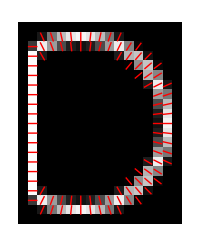

-Graphics3D-

```mathematica
smp=guvOnGlass[3µLensPitch,5µLensPitch,voxPitch,2,1];
Print[smp[[1,1]],smp[[1,2]],smp[[1,3]],smp[[1,4]],smp[[1,5]],smp[[1,6]],smp[[1,7]],smp[[1,8]],smp[[1,9]],smp[[1,10]],", bounding box=",smp[[2]]];
tmpI=Image3D[Reverse[smp[[3]],{1,2}]]
tmp1=Ceiling[smp[[2,3]]/voxPitch/2];  (*take a horizontal slice at z-position tmp1*)
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{i-0.5,j-0.5}-Drop[smp[[4,tmp1,j,i,1]],-1]/2,{i-0.5,j-0.5}+Drop[smp[[4,tmp1,j,i,1]],-1]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch}],1],Null];
Graphics[{Raster[ImageData[tmpI][[tmp1]]],If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]},ImageSize->200]
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[4,k,j,i,1]]/2,{i-0.5,j-0.5,k-0.5}+smp[[4,k,j,i,1]]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],1];
	Graphics3D[{Red,Map[Line,tmp2]},ImageSize->200]]
```

#### Enlarging and saving sample space

```mathematica
Max[smp[[3]]]
```

0.957111

```mathematica
Dimensions[smp[[3]]]
```

{33,33,33}

```mathematica
objDim={33,33,33};(*enter size of object space in voxels, {17,17,17}*)
pad=Floor[(objDim-Dimensions[smp[[3]]])/2];
Dimensions[object=Transpose[ArrayPad[smp[[3]],pad],{2,3,1}]]  (*Transpose[objectArray,{2,3,1}] rotates the object so that the viewing direction, after exporting, is perpendicular to the slices in ImageJ*)
Graphics3D[Raster3D[object,ColorFunction->"GrayLevelOpacity"]]
```

{33,33,33}

-Graphics3D-

```mathematica
Export["vP0.577_Object.tif",Image3D[object],"BitDepth"->8]
```

```mathematica
SetDirectory["/Users/rudolfo/LightFieldMicroscopy/Dresden_2020/Simulated Light Fields/guv_5µLP_1vP_vP_dip0"]
```

#### Creating a 3-dimensional object Array, in which each voxel includes the number of fluorophores nrFluor and their uniform 3D orientation in form of a unit vector that points either towards or away from the GUV center and has coordinates {x,y,z}: voxel = {nrFluor, {x,y,z}}

```mathematica
Dimensions[smp[[3]]]
```

{9,25,9}

```mathematica
smp[[4,17,17,2]]
```

{{-1.,0.,0.},{0,0,0},{0,0,0}}

```mathematica
(*isotropic radiation*)
objDim={29,29,11};(*enter size of object space in voxels, {17,17,17} for the new laboratory frame of reference (optical axis of LF microscope along z-axis)*)
pad=Floor[(objDim-Dimensions[smp[[3]]])/2];
Dimensions[object=Transpose[ArrayPad[smp[[3]],pad],{2,3,1}]]  (*Transpose[objectArray,{2,3,1}] rotates the object so that the viewing direction, after exporting, is perpendicular to the slices in ImageJ*)
Graphics3D[Raster3D[object,ColorFunction->"GrayLevelOpacity"]]
```

{11,29,29}

-Graphics3D-

```mathematica
Export["55_0_Object.tif",Image3D[object],"BitDepth"->8]
```

55_0_Object.tif

```mathematica
Export[ToString[60]<>"_0_Object.tif",Image3D[object],"BitDepth"->8]
```

60_0_Object.tif

```mathematica
Do[
	smp=bundle[4voxPitch,8µLensPitch,i,0,1,0];
	objDim={29,29,11};(*enter size of object space in voxels, {17,17,17} for the new laboratory frame of reference (optical axis of LF microscope along z-axis)*)
	pad=Floor[(objDim-Dimensions[smp[[3]]])/2];
	object=Transpose[ArrayPad[smp[[3]],pad],{2,3,1}];  (*Transpose[objectArray,{2,3,1}] rotates the object so that the viewing direction, after exporting, is perpendicular to the slices in ImageJ*)
	Export[ToString[i]<>"_0_Object.tif",Image3D[object],"BitDepth"->8],
{i,60,175,5}]
```

```mathematica
(*with dipoles*)
objDim={27,27,11};(*enter size of object space in voxels, {17,17,17}*)
pad=Floor[(objDim-Dimensions[smp[[3]]])/2];
object=Table[{smp[[3,i,j,k]],RotateLeft[smp[[4,i,j,k,1]],1]},{i,Dimensions[smp[[3]]][[1]]},{j,Dimensions[smp[[3]]][[2]]},{k,Dimensions[smp[[3]]][[3]]}];
Dimensions[object=Transpose[ArrayPad[object,pad],{2,3,1}]]  (*Transpose[objectArray,{2,3,1}] rotates the object so that the viewing direction, after exporting, is perpendicular to the slices in ImageJ*)
Graphics3D[Raster3D[object[[All,All,All,1]],ColorFunction->"GrayLevelOpacity"]]
tmp2=DeleteCases[Flatten[Table[{{i-0.5,j-0.5,k-0.5}-object[[k,j,i,2]]/2,{i-0.5,j-0.5,k-0.5}+object[[k,j,i,2]]/2},
			{i,Dimensions[object][[1]]},{j,Dimensions[object][[2]]},{k,Dimensions[object][[3]]}],2],Null];
Graphics3D[{Red,Map[Line,tmp2]},ImageSize->300]
```

```mathematica
object[[17,17,2]]
```

{0.952199,{-1.,0.,0.}}

```mathematica
Export["Object.json",object]
```

Object.json

```mathematica
SetDirectory["/Users/rudolfo/LightFieldMicroscopy/Dresden_2020/Simulated Light Fields/bundle_4vP_8µLP_vP0.577_azim_0_iso"]
```

/Users/rudolfo/LightFieldMicroscopy/Dresden_2020/Simulated Light Fields/bundle_4vP_8µLP_vP0.577_azim_0_iso

#### Not completed sample objects

#### Torus, torus[radius1,radius2Max,radius2Min,rotAngle,dip], radius1 is radius of the tube center line, r2Max-r2Min is the thickness of the tube wall

#### Notes

Wikipedia:
A torus can be defined parametrically by:
x(θ, ϕ ) = (R + r cosθ) cosϕ⁡
y(θ, ϕ ) = (R + r cosθ) sinϕ⁡
z(θ, ϕ ) = r sinθ
where
θ, φ are angles which make a full circle, so that their values start and end at the same point,
R (r1) is the distance from the center of the tube to the center of the torus,
r (r2) is the radius of the tube.

RO: 
To include the interior to the torus region, r2 varies between 0 and r2Max, or between r2Min and r2Max for a hollow torus.
The torus can be rotated by rotAngle [deg] around the vertical z-Axis. For rotAngle=0, the torus lies in the y-z plane

```mathematica
torus[radius1_,radius2Max_,radius2Min_,rotAngle_,dip_]:=
Module[{r1,r2Max,r2Min,rot,tBounds,rSize,tRegion, tArray,dipVec},
r1=Round[radius1/voxPitch]voxPitch; 
r2Max=(Round[radius2Max/voxPitch]+0.5)voxPitch;  (*if the center of radius1 is in the center of a voxel, the 0.5 ensures that radius2 reaches the edge of a voxel in x,y,z directions*)
r2Min=Round[radius2Min/voxPitch]voxPitch;  (*r2Max-r2Min is the thickness of the torus wall*)
rot=RotationTransform[rotAngle Degree,{0,0,1}];
tRegion=Region@ParametricRegion[{r2Inc Sin[θ],(r1+r2Inc Cos[θ]) Cos[ϕ],(r1+r2Inc Cos[θ]) Sin[ϕ]},{{ϕ,0,2Pi},{θ,0,2Pi},{r2Inc,r2Min,r2Max}}];
tRegion=Region@TransformedRegion[tRegion,rot];
tBounds=RegionBounds[tRegion];
rSize=Ceiling[(Transpose[tBounds][[2]]-Transpose[tBounds][[1]])/voxPitch];
tArray=Clip[Reverse[ImageData[RegionImage[tRegion,RegionBounds[tRegion],RasterSize->rSize]],{1,2}],{0,Infinity}];
If[dip==1,dipVec=Table[If[tArray[[k,j,i]]>0,tmp=({i-0.5,j-0.5,k-0.5}-rSize/2)×rot[{1,0,0}];tmp/Norm[tmp],{0,0,0}],{k,rSize[[3]]},{j,rSize[[2]]},{i,rSize[[1]]}],Null];
{{"Torus center {X,Y,Z}=",rSize voxPitch/2,", radius1=",r1,", radius2Max=",r2Max,", radius2Min=",r2Min,", voxPitch=",voxPitch,", rotation angle=",rotAngle,"°",", dipole flag=",dip},rSize voxPitch,tArray,dipVec}]
```

Graphics

Torus center {X,Y,Z}={20.125,20.125,25.375}, radius1=19.25, radius2Max=6.125, radius2Min=1.75, voxPitch=1.75, rotation angle=45°, dipole flag=1

bounding box={40.25,40.25,50.75}

-Graphics3D-

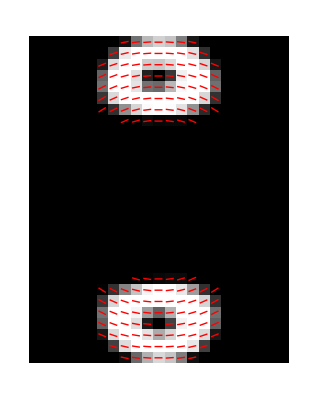

-Graphics3D-

```mathematica
smp=torus[20,5,1,45,1];
Print@@smp[[1]];Print["bounding box=",smp[[2]]];
Graphics3D[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"]]
tmp1=Ceiling[smp[[2,1]]/voxPitch/2];  (*take a vertical slice at x-position tmp1*)
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{j-0.5,k-0.5}-Drop[smp[[4,k,j,tmp1]],1]/2,{j-0.5,k-0.5}+Drop[smp[[4,k,j,tmp1]],1]/2},
			{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],1],Null];
Graphics[{Raster[smp[[3,All,All,Dimensions[smp[[3]]][[3]]/2//Ceiling]]],If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]}]
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[4,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[4,k,j,i]]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],1],Null];
Graphics3D[{If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]},ImageSize->300]
```

```mathematica
Dimensions[smp[[4]]]
```

{29,23,23,3}

#### Helix, helix[radius1,radius2Max,radius2Min,pitch,rotAngle,dip], radius1 is radius of the helical line, r2Max-r2Min is the thickness of the helix wall, pitch is the repeat distance per turn along helix center axis

#### Notes

A helix can be defined parametrically by:
x(θ, ϕ ) = (R + r cosθ) cosϕ⁡
y(θ, ϕ ) = (R + r cosθ) sinϕ⁡
z(θ, ϕ ) = r sinθ + p•ϕ/2π
where
θ, φ are angles which make a full circle, so that their values start and end at the same point,
R (r1) is the distance from the center of the helical tube to the helix axis,
r (r2) is the radius of the tube,
p is the pitch of the helix per turn
z is the helix axis

To include the interior to the helix region, r2 varies between 0 and r2Max, or between r2Min and r2Max for a hollow helix.
The torus can be rotated by rotAngle [deg] around the vertical z-Axis. For rotAngle=0, the torus lies in the y-z plane

```mathematica
helix[radius1_, radius2Max_, radius2Min_, pitch_,turns_, rotAngle_, dip_] :=
 Module[{r1, r2Max, r2Min, ptch, sS, rot, hBounds, rSize, tRegion, tArray, dipVec},
  r1 = Round[radius1/voxPitch] voxPitch; 
  r2Max = (Round[radius2Max/voxPitch] + 0.5) voxPitch;  (*if the center of radius1 is in the center of a voxel, the 0.5 ensures that radius2 reaches the edge of a voxel in x,y,z directions*)
  r2Min = Round[radius2Min/voxPitch] voxPitch;  (*r2Max-r2Min is the thickness of the torus wall*)
  ptch = Round[pitch/voxPitch] voxPitch;
  rot = RotationTransform[rotAngle Degree, {0, 0, 1}];
  tRegion = Region@ParametricRegion[{r2Inc Sin[θ] + pS  ϕ/(2 Pi), (r1 (1+spiral ϕ/(2 Pi)) + r2Inc Cos[θ]) Cos[ϕ], (r1 (1+spiral ϕ/(2 Pi)) + r2Inc Cos[θ]) Sin[ϕ]}, {{ϕ, 0, 2 Pi}, {θ, 0, 2 Pi}, {r2Inc, r2Min, r2Max}}]]
```

Graphics

```mathematica
smp=torus[20,5,1,45,1];
Print@@smp[[1]];Print["bounding box=",smp[[2]]];
Graphics3D[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"]]
tmp1=Ceiling[smp[[2,1]]/voxPitch/2];  (*take a vertical slice at x-position tmp1*)
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{j-0.5,k-0.5}-Drop[smp[[4,k,j,tmp1]],1]/2,{j-0.5,k-0.5}+Drop[smp[[4,k,j,tmp1]],1]/2},
			{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],1],Null];
Graphics[{Raster[smp[[3,All,All,Dimensions[smp[[3]]][[3]]/2//Ceiling]]],If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]}]
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[4,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[4,k,j,i]]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],1],Null];
Graphics3D[{If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]},ImageSize->300]
```

Torus center {X,Y,Z}={20.125,20.125,25.375}, radius1=19.25, radius2Max=6.125, radius2Min=1.75, voxPitch=1.75, rotation angle=45 [deg], dipole flag=1

bounding box={40.25,40.25,50.75}

-Graphics3D-

-Graphics-

-Graphics3D-

```mathematica
Dimensions[smp[[4]]]
```

{29,23,23,3}

```mathematica
voxPitch=1.75;
r1=Round[40/voxPitch]voxPitch; 
r2Max=(Round[4/voxPitch]+0.5)voxPitch;  (*if the center of radius1 is in the center of a voxel, the 0.5 ensures that radius 2 reaches the edge of a voxel in x,y,z directions*)
r2Min=Round[0/voxPitch]voxPitch;  (*r2Max-r2Min is the wall thickness of a hollow helix or spiral*)
hRegion=Table[Region@ParametricRegion[{r2Inc Sin[θ]+40 ϕ/(2Pi),(r1(0.5+ϕ/(2Pi))+r2Inc Cos[θ]) Cos[ϕ],(r1(0.5+ϕ/(2Pi))+r2Inc Cos[θ]) Sin[ϕ]},{{ϕ,2(i-1)Pi,2 i Pi},{θ,0,2Pi},{r2Inc,r2Min,r2Max}}],{i,2}];
```

```mathematica
hRegion[[1]]
```

-Graphics3D-

```mathematica
Region[RegionUnion[hRegion[[1]],hRegion[[2]]]]
```

-Graphics3D-

```mathematica
RegionBounds[%]
```

{{0.,80.},{-84.0196,64.1865},{-93.9477,74.0982}}

#### Spiral, helix[radius1,radius2Max,radius2Min,pitch,rotAngle,dip], radius1 is radius of the helical line, r2Max-r2Min is the thickness of the helix wall, pitch is the repeat distance per turn along helix center axis

#### Notes

A helix can be defined parametrically by:
x(θ, ϕ ) = (R + r cosθ) cosϕ⁡
y(θ, ϕ ) = (R + r cosθ) sinϕ⁡
z(θ, ϕ ) = r sinθ + p•ϕ/2π
where
θ, φ are angles which make a full circle, so that their values start and end at the same point,
R (r1) is the distance from the center of the helical tube to the helix axis,
r (r2) is the radius of the tube,
p is the pitch of the helix per turn
z is the helix axis

To include the interior to the helix region, r2 varies between 0 and r2Max, or between r2Min and r2Max for a hollow helix.
The helix can be rotated by rotAngle [deg] around the vertical z-Axis. For rotAngle=0, the torus lies in the y-z plane

A spiral is a helix with increasing radius R (r1). For example, R increases linearly with ϕ

```mathematica
(*The spiralInc parameter is the factor by witch r1 increases with every turn of the spiral; spiralInc=0 generates a helix*)
spiral[radius1_, radius2Max_, radius2Min_, pitch_, spiralInc_,turns_, rotAngle_, dip_] :=
 Module[{r1, r2Max, r2Min, pS, sS, rot, tBounds, rSize, tRegion, tArray, dipVec},
  r1 = Round[radius1/voxPitch] voxPitch; 
  r2Max = (Round[radius2Max/voxPitch] + 0.5) voxPitch;  (*if the center of radius1 is in the center of a voxel, the 0.5 ensures that radius2 reaches the edge of a voxel in x,y,z directions*)
  r2Min = Round[radius2Min/voxPitch] voxPitch;  (*r2Max-r2Min is the thickness of the torus wall*)
  pS = Round[pitch/voxPitch] voxPitch;
  rot = RotationTransform[rotAngle Degree, {0, 0, 1}];
  tRegion = Region@ParametricRegion[{r2Inc Sin[θ] + pS  ϕ/(2 Pi), (r1 (1+spiralInc ϕ/(2 Pi)) + r2Inc Cos[θ]) Cos[ϕ], (r1 (1+spiralInc ϕ/(2 Pi)) + r2Inc Cos[θ]) Sin[ϕ]}, {{ϕ, 0, 2 Pi}, {θ, 0, 2 Pi}, {r2Inc, r2Min, r2Max}}]]
```

Graphics

```mathematica
smp=torus[20,5,1,45,1];
Print@@smp[[1]];Print["bounding box=",smp[[2]]];
Graphics3D[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"]]
tmp1=Ceiling[smp[[2,1]]/voxPitch/2];  (*take a vertical slice at x-position tmp1*)
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{j-0.5,k-0.5}-Drop[smp[[4,k,j,tmp1]],1]/2,{j-0.5,k-0.5}+Drop[smp[[4,k,j,tmp1]],1]/2},
			{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],1],Null];
Graphics[{Raster[smp[[3,All,All,Dimensions[smp[[3]]][[3]]/2//Ceiling]]],If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]}]
If[smp[[1,-1]]≠0,tmp2=Flatten[Table[{{i-0.5,j-0.5,k-0.5}-smp[[4,k,j,i]]/2,{i-0.5,j-0.5,k-0.5}+smp[[4,k,j,i]]/2},
			{i,smp[[2,1]]/voxPitch},{j,smp[[2,2]]/voxPitch},{k,smp[[2,3]]/voxPitch}],1],Null];
Graphics3D[{If[smp[[1,-1]]≠0,{Red,Map[Line,tmp2]},Null]},ImageSize->300]
```

Torus center {X,Y,Z}={20.125,20.125,25.375}, radius1=19.25, radius2Max=6.125, radius2Min=1.75, voxPitch=1.75, rotation angle=45 [deg], dipole flag=1

bounding box={40.25,40.25,50.75}

-Graphics3D-

-Graphics-

-Graphics3D-

```mathematica
Dimensions[smp[[4]]]
```

{29,23,23,3}

```mathematica
r1=Round[40/voxPitch]voxPitch; 
r2Max=(Round[4/voxPitch]+0.5)voxPitch;  (*if the center of radius1 is in the center of a voxel, the 0.5 ensures that radius 2 reaches the edge of a voxel in x,y,z directions*)
r2Min=Round[0/voxPitch]voxPitch;  (*r2Max-r2Min is the wall thickness of a hollow helix or spiral*)
spiralInc=0;
(*hRegion=Table[Region@ParametricRegion[{r2Inc Sin[θ]+r1 ϕ/(2Pi),(r1(1+spiralInc ϕ/(2Pi))+r2Inc Cos[θ]) Cos[ϕ],(r1(1+spiralInc ϕ/(2Pi))+r2Inc Cos[θ]) Sin[ϕ]},{{ϕ,2(i-1)Pi,2 i Pi},{θ,0,2Pi},{r2Inc,r2Min,r2Max}}],{i,2}];*)
h1=Region@ParametricRegion[{r2Inc Sin[θ]+r1 ϕ/(2Pi),(r1(1+spiralInc ϕ/(2Pi))+r2Inc Cos[θ]) Cos[ϕ],(r1(1+spiralInc ϕ/(2Pi))+r2Inc Cos[θ]) Sin[ϕ]},{{ϕ,0Pi,2 Pi},{θ,0,2Pi}}];
h2=Region@ParametricRegion[{r2Inc Sin[θ]+r1 ϕ/(2Pi),(r1(1+spiralInc ϕ/(2Pi))+r2Inc Cos[θ]) Cos[ϕ],(r1(1+spiralInc ϕ/(2Pi))+r2Inc Cos[θ]) Sin[ϕ]},{{ϕ,2Pi,4 Pi},{θ,0,2Pi}}];
```

```mathematica
,{r2Inc,r2Min,r2Max}
```

```mathematica
RegionUnion[h1,h2]
```

-Graphics3D-

```mathematica
h1
```

-Graphics3D-

```mathematica
r2Inc=r2Max;
ParametricPlot3D[{r2Inc Sin[θ]+r1 ϕ/(2Pi),(r1(1+spiralInc ϕ/(2Pi))+r2Inc Cos[θ]) Cos[ϕ],(r1(1+spiralInc ϕ/(2Pi))+r2Inc Cos[θ]) Sin[ϕ]},{ϕ,0Pi,2 Pi},{θ,0,2Pi}]
```

-Graphics3D-

```mathematica
Subscript[ℛ, 1]=BooleanRegion[Or,{h1,h2}]
```

BooleanRegion[#1||#2&,{-Graphics3D-,-Graphics3D-}]

```mathematica
Region[%]
```

-Graphics3D-

```mathematica
RegionImage[Subscript[ℛ, 1]]
```

RegionImage::drf: RegionImage was unable to discretize the region BooleanRegion[#1||#2&,{Region[ParametricRegion[{{6.40599 ϕ+r2Inc Sin[«1»],Cos[ϕ] (40.25+Times[«2»]),(40.25+Times[«2»]) Sin[ϕ]},0≤ϕ≤2 π&&0≤θ≤2 π&&0.≤r2Inc≤4.375},{ϕ,θ,r2Inc}]],Region[ParametricRegion[{{6.40599 ϕ+r2Inc Sin[«1»],Cos[ϕ] (40.25+Times[«2»]),(40.25+Times[«2»]) Sin[ϕ]},2 π≤ϕ≤4 π&&0≤θ≤2 π&&0.≤r2Inc≤4.375},{ϕ,θ,r2Inc}]]}].

RegionImage[BooleanRegion[#1||#2&,{-Graphics3D-,-Graphics3D-}]]

```mathematica
TransformedRegion[h1,TranslationTransform[{r1,0,0}]]
```

-Graphics3D-

```mathematica
RegionImage[h1]
```

BoundaryMeshRegion::binsect: The boundary curves self-intersect or cross each other in BoundaryMeshRegion[{{17.8791,-44.4188,6.70663},{14.0439,-32.9262,30.5561},{19.167,-44.6144,6.73184},{15.334,-33.0613,30.6994},{19.1628,-44.4103,6.68589},«42»,{7.91462,-7.19835,42.7427},{7.13224,-7.00524,41.3308},{7.24265,-9.39881,39.4071},«1764»},{{},{},{Polygon[{«1»}]}}].

$Aborted[]

```mathematica
RegionImage[hRegion2]
```

-Graphics3D-

```mathematica
ImageAdd[%109,%116]
```

-Graphics3D-

```mathematica
hRegion1
```

-Graphics3D-

```mathematica
RegionBounds[%]
```

{{0.,40.25},{-44.625,44.625},{-44.625,44.625}}

```mathematica
hRegion2
```

-Graphics3D-

```mathematica
RegionBounds[%]
```

{{0.,60.375},{-44.625,44.625},{-44.625,44.625}}

```mathematica
RegionUnion[h1,TransformedRegion[h1,TranslationTransform[{r1/2,0,0}]]]
```

-Graphics3D-

```mathematica
RegionUnion[-Graphics3D-,-Graphics3D-]
```

-Graphics3D-

```mathematica
RegionBounds[%]
```

{{-0.996616,1.},{-1.,1.},{-1.,1.}}

### Generating light field images

The output is image intensities
All distances in microns

```mathematica
(*Sample store*)
smp=ball[0,0,0,1,0];jjkkMinMax=Round[{-5,5,-5,5}];
smp=guv[µLensPitch,voxPitch,1,0];jjkkMinMax=Round[{-2,2,-2,2}];
smp=membranePatch[15µLensPitch,voxPitch,0,0,1,0];jjkkMinMax=Round[{-12,12,-12,12}];  (*e.g. for radiometry image*)
smp=bundle[1,30,90,0,1,0];jjkkMinMax=Round[{-3,3,-12,12}];
smp=guvOnGlass[13.5,22,voxPitch,2,0];jjkkMinMax=Round[{-16,16,-16,16}];(*number of microlenses in y- and z-direction; the larger the object the more microlenses*)
smp=torus[20,5,1,0,0];jjkkMinMax=Round[{-20,20,-20,20}];
```

#### Attempt to use compiled code (unsuccessful)

```mathematica
(*I have tried to replace the expression Plus@@(Extract[objectArray,tmp2]×iL[[ii]]) in*)
camArray[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Plus@@(Extract[objectArray,tmp2]×iL[[ii]])
(*with the compiled version (see above):*)
camArray[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=camArrayCmpld[objectArray,tmp2,iL[[ii]]]
(*but it produced the following error message *)
CompiledFunction::cfex: "Could not complete external evaluation at instruction \!\(\*RowBox[{\"1\"}]\); proceeding with uncompiled evaluation."

(*I think a problem is the varying length of the tensor elements  tmp2 and iL[[ii]]*)
```

```mathematica
Depth[objectArray]
```

3

```mathematica
camArrayCmpld=Compile[{{objectArray,_Real,3},{tmp2,_Integer,2},{iLii,_Real,1}},Plus@@(Extract[objectArray,tmp2]×iLii)]
```

CompiledFunction[…]

#### Uncompiled code

```mathematica
smp=guv[5µLensPitch,voxPitch,1,0];jjkkMinMax=Round[{-12,12,-12,12}];(*number of microlenses in y- and z-direction; the larger the object the more microlenses*)
displace={0µLensPitch,0voxPitch,0voxPitch};(*displac sample from voxCtr*)
polSettings=4; (*number of polarizer settings, either 2 (0°, 90°) or 4 (0°, 135°, 90°, 45°)*)
```

```mathematica
(*Comment out Graphics3D[objectArray] for voxPitch smaller than 1.73µm*)
Print@@smp[[1]];
subµLns=Floor[µLensPitch/(2voxPitch)];
thisRayEnter=Table[tmp=rayEnter[[i]]+(voxCtr[[1]]+(-smp[[2,1]]/2+displace[[1]]))/voxCtr[[1]](voxCtr-rayEnter[[i]]);{0,tmp[[2]],tmp[[3]]},{i,nrRays}];
thisRayExit=Table[tmp=rayEnter[[i]]+(voxCtr[[1]]+(smp[[2,1]]/2+displace[[1]]))/voxCtr[[1]](voxCtr-rayEnter[[i]]);{smp[[2,1]],tmp[[2]],tmp[[3]]},{i,nrRays}];
(*smpBoxNrs0 is the space centered on voxCtr that includes the index depth of the sample along X and the Y and Z voxPitch index ranges that include all µLenses with rays that interact with the sample*)
smpBoxNrs0=Transpose[{{0,voxCtr[[2]]-smp[[2,2]]/2,voxCtr[[3]]-smp[[2,3]]/2},{smp[[2,1]],voxCtr[[2]]+smp[[2,2]]/2,voxCtr[[3]]+smp[[2,3]]/2}}+(Abs[displace[[1]]]+smp[[2,1]]/2){{0,-Tan[ArcSin[naObj/nMedium]],-Tan[ArcSin[naObj/nMedium]]},{0,Tan[ArcSin[naObj/nMedium]],Tan[ArcSin[naObj/nMedium]]}}]/voxPitch//Round;
(*smpBoxNrs identifies the space in index numbers that has the sample object inside*)
(*For smpBoxNrs and sampBoxNrs0, the X-index is 0 where the object starts and extends in X to the end of the object*)
smpBoxNrs=Transpose[{tmp1=voxCtr+displace-smp[[2]]/2;{0,tmp1[[2]],tmp1[[3]]},tmp2=voxCtr+displace+smp[[2]]/2;{smp[[2,1]],tmp2[[2]],tmp2[[3]]}}]/voxPitch//Round;
(*smpBoxNrsPrint shows in global indices the box coordinates that contains the object, including its displacement if any*)
smpBoxNrsPrint=Transpose[{voxCtr+displace-smp[[2]]/2,voxCtr+displace+smp[[2]]/2}]/voxPitch//Round;
Print["sample box = ",smpBoxNrsPrint, " [numbers]"];
objectArray=ArrayPad[smp[[3]],Transpose[(Transpose[Reverse[smpBoxNrs]]-{{0,0,0},{voxNrYZ,voxNrYZ,smp[[2,1]]/voxPitch//Round}}){1,-1}]];
(*If[smp[[1,-1]]==1,tmp=.;objectArrayDipVec=ArrayPad[smp[[4]],Transpose[(Transpose[Reverse[smpBoxNrs]]-{{0,0,0},{voxNrYZ,voxNrYZ,smp[[2,1]]/voxPitch//Round}}){1,-1}],tmp]/.tmp->{0,0,0},Null];*)
If[smp[[1,-1]]≠0,tmp=.;objectArrayDipVec=ArrayPad[smp[[4]],Transpose[(Transpose[Reverse[smpBoxNrs]]-{{0,0,0},{voxNrYZ,voxNrYZ,smp[[2,1]]/voxPitch//Round}}){1,-1}],tmp]/.tmp->{{0,0,0},{0,0,0},{0,0,0}},Null];
Graphics3D[{Translate[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"],(voxCtr+displace-smp[[1,2]])/voxPitch],Blue,Line[{rayEnter[[1]],rayExit[[1]]}/voxPitch],Line[{rayEnter[[159]],rayExit[[159]]}/voxPitch],Line[{rayEnter[[75]],rayExit[[75]]}/voxPitch],Line[{rayEnter[[89]],rayExit[[89]]}/voxPitch]},PlotRange->{{0,voxNrX},{0,voxNrYZ},{0,voxNrYZ}},ViewPoint->{0,-Infinity,0}]
rayEnterCamPix=Table[camRayEntrance[[i,1]],{i,nrRays}]; (*List of {i,j} coordinates of camera pixels that correspond to rays that enter object space*)
mP0=Table[midPoints[thisRayEnter[[i]],thisRayExit[[i]],voxPitchList,smpBoxNrs0],{i,nrRays}];(*list of midPoint lists for every ray within naObj centered on voxCtr*)
iL=Table[intersectLength[thisRayEnter[[i]],thisRayExit[[i]],voxPitchList,smpBoxNrs0],{i,nrRays}];(*list of intersectLength lists for every ray within naObj centered on voxCtr; this list remains the same even when the µLens is shifted in y- and z-direction*)
Print["dip flag = ",smp[[1,-1]]];
Timing[Monitor[
If[smp[[1,-1]]==0,
	camArray=Table[0,{i,nrCamPix},{j,nrCamPix}];
	lfImageArray=Table[
		Do[mP0ii=Plus[#,{0,jj µLensPitch,kk µLensPitch}]&/@mP0[[ii]]; (*moving the midPoints by increments of µLensPitch*)
			camArray[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0;
			Do[mP=Plus[#,{0,jjj voxPitch,kkk voxPitch}]&/@mP0ii; (*moving the midPoints by increments of voxPitch within a µLensPitch*)
					tmp2=Ceiling[Reverse[mP,2]/voxPitch];  (*Reverse[mP,2] puts the part identifier in the right order [[k,j,i]]*)
					tmp3=Extract[objectArray,tmp2];
(*					camArray[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Plus@@(tmp3×iL[[ii]]),*)
					camArray[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Sum[tmp3[[i]]×iL[[ii,i]],{i,Length[iL[[ii]]]}],
			{jjj,-subµLns,subµLns},{kkk,-subµLns,subµLns}],
		{ii,nrRays}];
		Image[camArray,ImageSize->32],
	{jj,jjkkMinMax[[1]],jjkkMinMax[[2]]},{kk,jjkkMinMax[[3]],jjkkMinMax[[4]]}]];
If[smp[[1,-1]]≠0,
	rayAmpVecList=Table[{0,0,0},{i,nrCamPix},{j,nrCamPix}];
	camArrayY=Table[0,{i,nrCamPix},{j,nrCamPix}];  (*initializations of array of tomographic pixels behind a single microlens (camArray) and the light field array (lfArray)*)
	camArrayZ=Table[0,{i,nrCamPix},{j,nrCamPix}];
	lfImageArrayY=Table[0,{jj,jjkkMinMax[[2]]-jjkkMinMax[[1]]+1},{kk,jjkkMinMax[[4]]-jjkkMinMax[[3]]+1}];
	lfImageArrayZ=Table[0,{jj,jjkkMinMax[[2]]-jjkkMinMax[[1]]+1},{kk,jjkkMinMax[[4]]-jjkkMinMax[[3]]+1}];
	If[polSettings==4,
		camArrayYZ=Table[0,{i,nrCamPix},{j,nrCamPix}];
		camArrayZY=Table[0,{i,nrCamPix},{j,nrCamPix}];
		lfImageArrayYZ=Table[0,{jj,jjkkMinMax[[2]]-jjkkMinMax[[1]]+1},{kk,jjkkMinMax[[4]]-jjkkMinMax[[3]]+1}];
		lfImageArrayZY=Table[0,{jj,jjkkMinMax[[2]]-jjkkMinMax[[1]]+1},{kk,jjkkMinMax[[4]]-jjkkMinMax[[3]]+1}];
		unitYZ=Normalize[{0,1,1}];
		unitZY=Normalize[{0,-1,1}]];
		rayUnitVectorYZ=Table[Normalize[rayUnitVectors[[ii,2]]+rayUnitVectors[[ii,3]]],{ii,Length[rayEnterCamPix]}];
		rayUnitVectorZY=Table[Normalize[rayUnitVectors[[ii,2]]-rayUnitVectors[[ii,3]]],{ii,Length[rayEnterCamPix]}]];
If[smp[[1,-1]]==1,
	Do[
		Do[mP0ii=Plus[#,{0,jj µLensPitch,kk µLensPitch}]&/@mP0[[ii]]; (*moving the midPoints by increments of µLensPitch*)
			rayAmpVecList[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]={0,0,0};
(*			camArrayY[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0;
			camArrayZ[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0;*)
			If[polSettings==4,
				camArrayYZ[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0;
				camArrayZY[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0];
			Do[mP=Plus[#,{0,jjj voxPitch,kkk voxPitch}]&/@mP0ii; (*moving the midPoints by increments of voxPitch within a µLensPitch*)
				tmp2=Ceiling[Reverse[mP,2]/voxPitch];  (*Reverse[mP,2] puts the part identifier in the right order [[k,j,i]]*)
(*				camArrayY[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Plus@@(Extract[objectArray,tmp2]×Power[(Extract[objectArrayDipVec,tmp2].rayUnitVectors[[ii,2]])//Chop,2]×iL[[ii]]);
				camArrayZ[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Plus@@(Extract[objectArray,tmp2]×Power[(Extract[objectArrayDipVec,tmp2].rayUnitVectors[[ii,3]])//Chop,2]×iL[[ii]]);*)
				rayAmpVecList[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=rayUnitVectors[[ii,4]].#&/@(Plus@@(Extract[objectArray,tmp2]×Extract[objectArrayDipVec,tmp2]×iL[[ii]])),(*electric field vector (amplitudes) of ray ii after its direction is rotated parallel to x-direction; rayUnitVectors[[ii,4]] is the rotation matrix*)
			{jjj,-subµLns,subµLns},{kkk,-subµLns,subµLns}],
		{ii,nrRays}];
		Do[camArrayY[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=Power[rayAmpVecList[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]],2]]/Power[2subµLns+1,2],2];
			camArrayZ[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=Power[rayAmpVecList[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]],3]]/Power[2subµLns+1,2],2];
			If[polSettings==4,
				camArrayYZ[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Power[rayAmpVecList[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]].unitYZ/Power[2subµLns+1,2],2];
				camArrayZY[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Power[rayAmpVecList[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]].unitZY/Power[2subµLns+1,2],2]],
		{ii,nrRays}];
		jjLF=jj-jjkkMinMax[[1]]+1;kkLF=kk-jjkkMinMax[[3]]+1;
		lfImageArrayY[[jjLF,kkLF]]=Image[camArrayY,ImageSize->32];
		lfImageArrayZ[[jjLF,kkLF]]=Image[camArrayZ,ImageSize->32];
		If[polSettings==4,
			lfImageArrayYZ[[jjLF,kkLF]]=Image[camArrayYZ,ImageSize->32];
			lfImageArrayZY[[jjLF,kkLF]]=Image[camArrayZY,ImageSize->32]],
	{jj,jjkkMinMax[[1]],jjkkMinMax[[2]]},{kk,jjkkMinMax[[3]],jjkkMinMax[[4]]}]];
If[smp[[1,-1]]==2,
	Do[
		Do[mP0ii=Plus[#,{0,jj µLensPitch,kk µLensPitch}]&/@mP0[[ii]]; (*moving the midPoints by increments of µLensPitch*)
			camArrayY[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0;
			camArrayZ[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0;
			If[polSettings==4,
				camArrayYZ[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0;
				camArrayZY[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]=0];
			Do[mP=Plus[#,{0,jjj voxPitch,kkk voxPitch}]&/@mP0ii; (*moving the midPoints by increments of voxPitch within a µLensPitch*)
				tmp2=Ceiling[Reverse[mP,2]/voxPitch];  (*Reverse[mP,2] puts the part identifier in the right order [[k,j,i]]*)
				camArrayY[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Plus@@(Extract[objectArray,tmp2]×Apply[Plus,Power[(Extract[objectArrayDipVec,tmp2].rayUnitVectors[[ii,2]])//Chop,2],2]×iL[[ii]]);
				camArrayZ[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Plus@@(Extract[objectArray,tmp2]×Apply[Plus,Power[(Extract[objectArrayDipVec,tmp2].rayUnitVectors[[ii,3]])//Chop,2],2]×iL[[ii]]);
				If[polSettings==4,
					camArrayYZ[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Plus@@(Extract[objectArray,tmp2]×Apply[Plus,Power[(Extract[objectArrayDipVec,tmp2].rayUnitVectorYZ[[ii]])//Chop,2],2]×iL[[ii]]);
					camArrayZY[[rayEnterCamPix[[ii,1]],rayEnterCamPix[[ii,2]]]]+=Plus@@(Extract[objectArray,tmp2]×Apply[Plus,Power[(Extract[objectArrayDipVec,tmp2].rayUnitVectorZY[[ii]])//Chop,2],2]×iL[[ii]])],
			{jjj,-subµLns,subµLns},{kkk,-subµLns,subµLns}],
		{ii,nrRays}];
		jjLF=jj-jjkkMinMax[[1]]+1;kkLF=kk-jjkkMinMax[[3]]+1;
		lfImageArrayY[[jjLF,kkLF]]=Image[camArrayY,ImageSize->32];
		lfImageArrayZ[[jjLF,kkLF]]=Image[camArrayZ,ImageSize->32];
		If[polSettings==4,
			lfImageArrayYZ[[jjLF,kkLF]]=Image[camArrayYZ,ImageSize->32];
			lfImageArrayZY[[jjLF,kkLF]]=Image[camArrayZY,ImageSize->32]],
	{jj,jjkkMinMax[[1]],jjkkMinMax[[2]]},{kk,jjkkMinMax[[3]],jjkkMinMax[[4]]}]];,
{"row = ",jj}]]
```

GUV center {X,Y,Z}={9.53333,9.53333,9.53333}, GUV radius=8.95556, membrane thick=0.577778, voxPitch=0.577778, ratio=1, dipole flag=0

sample box = {{200,233},{590,623},{590,623}} [numbers]

-Graphics3D-

dip flag = 0

{277.779,Null}

```mathematica
lfImage=ImageAssemble[Transpose[100lfImageArray]];
Print["voxPitch = ",voxPitch];
lfImage
Print["Image dimension = ",ImageDimensions[%]];
Print["Max = ",Max[ImageData[lfImage]]];
(*Histogram[ImageData[lfImage],PlotRange->All]*)
```

voxPitch = 0.577778

-Graphics-

Image dimension = {400,400}

Max = 3641.49

```mathematica
Graphics3D[{Translate[Raster3D[smp[[3]],ColorFunction->"GrayLevelOpacity"],(voxCtr+displace-smp[[1,2]])/voxPitch],Blue,Line[{rayEnter[[1]],rayExit[[1]]}/voxPitch],Line[{rayEnter[[159]],rayExit[[159]]}/voxPitch],Line[{rayEnter[[75]],rayExit[[75]]}/voxPitch],Line[{rayEnter[[89]],rayExit[[89]]}/voxPitch]},PlotRange->{{0,voxNrX},{0,voxNrYZ},{0,voxNrYZ}},ViewPoint->{0,-Infinity,0}]
```

-Graphics3D-

```mathematica
Export["175_0_LFImage.tif",lfImage/100,"BitDepth"->16]
```

175_0_LFImage.tif

```mathematica
SetDirectory["/Users/rudolfo/LightFieldMicroscopy/Dresden_2020/Simulated Light Fields/bundle_4vP_8µLP_vP0.577_azim_0_iso"]
```

```mathematica
lfImageY=ImageAssemble[Transpose[lfImageArrayY]];
Print["voxPitch = ",voxPitch];
lfImageY//ImageAdjust
Print["Image dimension = ",ImageDimensions[%]];
Print["Max = ",Max[ImageData[lfImageY]]];
(*Histogram[ImageData[lfImageY],PlotRange->All]*)
```

voxPitch = 0.576667

-Graphics-

Image dimension = {336,336}

Max = 31.477

```mathematica
lfImageZ=ImageAssemble[Transpose[lfImageArrayZ]];
Print["voxPitch = ",voxPitch];
lfImageZ//ImageAdjust
Print["Image dimension = ",ImageDimensions[%]];
Print["Max = ",Max[ImageData[lfImageZ]]];
(*Histogram[ImageData[lfImageZ],PlotRange->All]*)
```

voxPitch = 0.576667

-Graphics-

Image dimension = {336,336}

Max = 31.4604

```mathematica
lfImageYPlusZ=ImageAdd[lfImageY,lfImageZ];
lfImageYPlusZ//ImageAdjust
```

-Graphics-

```mathematica
lfImageYZ=ImageAssemble[Transpose[lfImageArrayYZ]];
Print["voxPitch = ",voxPitch];
lfImageYZ//ImageAdjust
Print["Image dimension = ",ImageDimensions[%]];
Print["Max = ",Max[ImageData[lfImageYZ]]];
(*Histogram[ImageData[lfImageYZ]]*)
```

voxPitch = 0.576667

-Graphics-

Image dimension = {336,336}

Max = 33.205

```mathematica
lfImageZY=ImageAssemble[Transpose[lfImageArrayZY]];
Print["voxPitch = ",voxPitch];
lfImageZY//ImageAdjust
Print["Image dimension = ",ImageDimensions[%]];
Print["Max = ",Max[ImageData[lfImageZY]]];
(*Histogram[ImageData[lfImageZY]]*)
```

voxPitch = 0.576667

-Graphics-

Image dimension = {336,336}

Max = 30.5299

```mathematica
lfImageYZPlusZY=ImageAdd[lfImageYZ,lfImageZY];
lfImageYZPlusZY//ImageAdjust
```

-Graphics-

```mathematica
ImageSubtract[lfImageYZPlusZY,lfImageYPlusZ]//ImageAdjust
Max[ImageData[ImageSubtract[lfImageYZPlusZY,lfImageYPlusZ]]]
```

-Graphics-

3.8147×10^-6

```mathematica
i1=ImageAssemble[Transpose[Drop[lfImageArray,0,1]]];
i2=ImageReflect[ImageAssemble[Transpose[Drop[lfImageArray,1,0]]],Left];
i3=ImageReflect[ImageAssemble[Transpose[Drop[lfImageArray,1,1]]],Left];
i4=ImageAssemble[{{ImageReflect[i1]},{lfImage}}];
i5=ImageAssemble[{{ImageReflect[i3]},{i2}}];
ImageAssemble[{i5,i4}]//ImageAdjust
```

```mathematica
ImageDimensions[%]
```

```mathematica
Export["pol0_LFImage.tif",lfImageY/34,"BitDepth"->8]
```

pol0_LFImage.tif

```mathematica
SetDirectory["/Users/rudolfo/LightFieldMicroscopy/Dresden_2020/Simulated Light Fields/guv_5µLP_1vP_vP0.577_dip0.2_2"]
```

/Users/rudolfo/LightFieldMicroscopy/Dresden_2020/Simulated Light Fields/guv_5µLP_1vP_vP0.577_dip0.2_2

### Results

#### guv[10, voxPitch, 0 and 1] with center in voxCtr, voxPitch=1.75µm

guv[10, voxPitch, 0], isotropic emission, intensities

guv[10, voxPitch, 1], dipole emitters

lfImageY, image intensities

lfImageZ, image intensities

lfImageY + lfImageZ, image intensities

#### membranePatch[10 and 40, voxPitch, 0 and 1] with center in voxCtr, voxPitch=1.75µm

guv[10, voxPitch, 0], isotropic emission, image intensities

guv[10, voxPitch, 1], dipole emitters

lfImageY, image intensities

lfImageZ, image intensities

lfImageY + lfImageZ, image intensities

guv[40, voxPitch, 0], isotropic emission, used for radiometry image

#### guvOnGlass[10, voxPitch, 0 and 1] with center in voxCtr, voxPitch=1.75µm

guvOnGlass[10, voxPitch, 0], isotropic emission, image intensities

guvOnGlass[10, voxPitch, 1], dipole emitters

lfImageY, image intensities

lfImageZ, image intensities

lfImageY + lfImageZ, image intensities

#### torus[20, 5, 1, 0, 0 and 1] with center in voxCtr, torus in y-z plane, voxPitch=1.75µm

torus[20, 5, 1, 0, 0], isotropic emission, image intensities

torus[20, 5, 1, 0, 1], dipole emitters

lfImageY, image intensities

lfImageZ, image intensities

lfImageY + lfImageZ, image intensities

#### torus[20, 5, 1, 90, 0 and 1] with center in voxCtr, torus in x-z plane, voxPitch=1.75µm

torus[20, 5, 1, 90, 0], isotropic emission, image intensities

torus[20, 5, 1, 90, 1], dipole emitters

lfImageY, image intensities

lfImageZ, image intensities

lfImageY + lfImageZ, image intensities

End of grouping

## Simulated objects and their light field images, isotropic fluorescence

### Giant Unilamellar Vesicle (GUV), guv[guvRadius,membraneThickness], all locations and distances in micron

#### guv[30,voxPitch] with center in voxCtr, voxPitch=1.75µm

-Graphics-

#### guv[30,voxPitch] with center displaced from voxCtr by {-guvRadius,0,0}}, voxPitch=1.75µm

-Graphics-

#### guv[30,voxPitch] with center in voxCtr, voxPitch=1.75/2=0.875µm

-Graphics-

#### guv[30,voxPitch] with center in voxCtr, voxPitch=1.75/4=0.4375µm

-Graphics-

```mathematica
smp=guv[30,voxPitch];
displace={0voxPitch,0voxPitch,0voxPitch};(*displacement from voxCtr*)
Print[smp[[1,1]],smp[[1,2]],smp[[1,3]],smp[[1,4]],smp[[1,5]],smp[[1,6]],", bounding box max=",smp[[2]]];
Image3D[smp[[3]]]
Image[ImageData[%][[Ceiling[smp[[2,2]]/voxPitch/2]]]]
```

GUV center={31.0625,31.0625,31.0625}, GUV radius=30.1875, membrane thick=0.875, bounding box max={62.125,62.125,62.125}

-Graphics3D-

-Graphics-

### GUV attached to glass surface, guvOnGlass[guvRadius,membraneThickness], all locations and distances in micron, voxPitch=1.75

#### guvOnGlass[30,voxPitch] with center in voxCtr

-Graphics-

```mathematica
smp=guvOnGlass[30,voxPitch];
Print[smp[[1,1]],smp[[1,2]],smp[[1,3]],smp[[1,4]],smp[[1,5]],smp[[1,6]],", bounding box max=",smp[[2]]];
Image3D[smp[[3]]]
Image[smp[[3]][[Ceiling[smp[[2,2]]/voxPitch/2]]]]
```

GUV center={}, GUV radius=30.625, membrane thick=1.75, bounding box max={36.75,64.75,64.75}

-Graphics3D-

-Graphics-

### Flat membrane patch on glass surface, membranePatch[patchRadius,membraneThickness], all locations and distances in micron, voxPitch=1.75

#### membranePatch[30,voxPitch] with center in voxCtr

-Graphics-

#### membranePatch[90,voxPitch] with center in voxCtr

-Graphics-

```mathematica
smp=membranePatch[30,voxPitch];
Print[smp[[1,1]],smp[[1,2]],smp[[1,3]],smp[[1,4]],smp[[1,5]],smp[[1,6]],", bounding box=",smp[[2]]];
Image3D[smp[[3]]]
Image[smp[[3]][[Ceiling[smp[[2,2]]/voxPitch/2]]]]//ImageAdjust
```

patch center={0.875,30.625,30.625}, patch radius=30.625, membrane thickness=1.75, bounding box={5.25,64.75,64.75}

-Graphics3D-

-Graphics-

### Cuboid Vesicle, cubeVes[sideLength,membraneThickness], all locations and distances in micron, , voxPitch=1.75

#### cubeVes[60,voxPitch] with center located in voxCtr

-Graphics-

#### cubeVes[60,voxPitch] with center displaced from voxCtr by {-sideLength/2,0,0}}, voxPitch=1.75µm

-Graphics-

```mathematica
smp=cubeVes[60,voxPitch];
Print[smp[[1,1]],smp[[1,2]],smp[[1,3]],smp[[1,4]],smp[[1,5]],smp[[1,6]],", bounding box max=",smp[[2]]];
Image3D[smp[[3]]]
Image[ImageData[%][[Ceiling[smp[[2,1]]/voxPitch/2]]]]
```

cubeVes center={32.375,32.375,32.375}, cubeVes side length=61.25, membrane thick=1.75, bounding box max={64.75,64.75,64.75}

-Graphics3D-

-Graphics-

### Bundles

```mathematica
voxPitch=25/16/3;
smp=bundle[3voxPitch,30µLensPitch,0,90];jjkkMinMax=Round[{-30,30,-30,30}];(*number of microlenses in y- and z-direction; the larger the object the more microlenses*)
displace={0µLensPitch,0voxPitch,0voxPitch};(*displacement from voxCtr*)
```

-Graphics-

## Experimental light field images of GUVs by Mai Tran

```mathematica
Import["/Users/rudolfo/LightFieldMicroscopy/Experiments/2019_04_24 Mai Tran GUV/reg_z8-Crop.tif"]//ImageAdjust
```

-Graphics-

```mathematica
Import["/Users/rudolfo/LightFieldMicroscopy/Experiments/2019_04_24 Mai Tran GUV/SMS_2019_0424_1415_image3_z8-Crop.tif"]//ImageAdjust
```

-Graphics-

```mathematica
Import["/Users/rudolfo/LightFieldMicroscopy/Experiments/2019_04_24 Mai Tran GUV/SMS_2019_0424_1415_image3_z18-Crop.tif"]//ImageAdjust
```

-Graphics-

```mathematica
Import["/Users/rudolfo/LightFieldMicroscopy/Experiments/2019_04_24 Mai Tran GUV/SMS_2019_0424_1415_image3_z1_on_coverslip-Crop.tif"]//ImageAdjust
```

-Graphics-

```mathematica
Import["/Users/rudolfo/LightFieldMicroscopy/Experiments/2019_04_24 Mai Tran GUV/SMS_2019_0424_1415_image3_z8-Crop2.tif"]//ImageAdjust
```

-Graphics-

```mathematica
Import["/Users/rudolfo/LightFieldMicroscopy/Experiments/2019_04_24 Mai Tran GUV/reg_z8-Crop2.tif"]//ImageAdjust
```

-Graphics-

## Notes on ImageData reversal and part specs for Raster3D arrays versus Image3D In Raster3D arrays, the part specification is [[z,y,x]] -Graphics3D-

The positions of image data  culled using ImageData[] from a 2D and 3D array need to be reversed when plotting with Raster3D[]

```mathematica
ImageData[-Graphics3D-]
```

{{{{0.4,0.,0.},{0.475,0.,0.},{0.55,0.,0.}},{{0.625,0.,0.},{0.7,0.,0.},{0.775,0.,0.}},{{1.,1.,1.},{0.925,0.,0.},{1.,0.,0.}}},{{{0.,0.4,0.},{0.,0.475,0.},{0.,0.55,0.}},{{0.,0.625,0.},{0.,0.7,0.},{0.,0.775,0.}},{{0.,0.85,0.},{0.,0.925,0.},{0.,1.,0.}}},{{{0.,0.,0.4},{0.,0.,0.475},{1.,1.,0.}},{{0.,0.,0.625},{0.,0.,0.7},{0.,0.,0.775}},{{0.,0.,0.85},{0.,0.,0.925},{0.,0.,1.}}}}

```mathematica
Image3D[%]
```

-Graphics3D-

When plotting the ImageData[] array with Raster3D[], the bottom right corner (yellow cube) becomes the top left corner with the same x-coordinate

```mathematica
Graphics3D[Raster3D[ImageData[-Graphics3D-]],Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Reverse[ImageData[],{1,2}] puts the cubes back in their places

```mathematica
Graphics3D[Raster3D[Reverse[ImageData[-Graphics3D-],{1,2}]],Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

For the default ViewPoint, the origin in Raster3D[] graphics is in the bottom left corner (darker blue cube), and the positive x-axis extends to the right, y-axis  towards the back, and z-axis up.
Also, in Raster3D[] arrays, the x-position is last in the part specification, in the middle is y, and the first position is the z-coordinate: [[z,y,x]]

In the data array for Graphics3D[], the white cube is part [[3,1,1]], and the yellow cube is [[1,3,3]] (RGB values of White and Yellow are {1,1,1} and {1,1,0}, respectively):

```mathematica
Reverse[ImageData[-Graphics3D-],{1,2}][[3,1,1]]
```

{1.,1.,1.}

```mathematica
Reverse[ImageData[-Graphics3D-],{1,2}][[1,3,3]]
```

{1.,1.,0.}

While in ImageData[], the white cube is part [[1,3,1]], and the yellow cube is [[3,1,3]]

```mathematica
ImageData[-Graphics3D-][[1,3,1]]
```

{1.,1.,1.}

```mathematica
ImageData[-Graphics3D-][[3,1,3]]
```

{1.,1.,0.}

```mathematica
arrayData=Reverse[ImageData[-Graphics3D-],{1,2}]
```

{{{{0.,0.,0.85},{0.,0.,0.925},{0.,0.,1.}},{{0.,0.,0.625},{0.,0.,0.7},{0.,0.,0.775}},{{0.,0.,0.4},{0.,0.,0.475},{1.,1.,0.}}},{{{0.,0.85,0.},{0.,0.925,0.},{0.,1.,0.}},{{0.,0.625,0.},{0.,0.7,0.},{0.,0.775,0.}},{{0.,0.4,0.},{0.,0.475,0.},{0.,0.55,0.}}},{{{1.,1.,1.},{0.925,0.,0.},{1.,0.,0.}},{{0.625,0.,0.},{0.7,0.,0.},{0.775,0.,0.}},{{0.4,0.,0.},{0.475,0.,0.},{0.55,0.,0.}}}}

The following gets a horizontal slice (x-y plane) from a 3D array:

```mathematica
Graphics3D[Raster3D[arrayData[[{1}]]],Axes->True,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

This gets y-z planes:

```mathematica
Graphics3D[Raster3D[arrayData[[All,All,{1,2}]]]]
```

-Graphics3D-

To draw it as an Image3D, the arrayData need to be reversed again

```mathematica
Image3D[Reverse[arrayData,{1,2}]]
```

-Graphics3D-

To build a Table[] with the part assignment suitable for display with Raster[], invert the part assignments as in Table[ ListElement, {k, kMax}, {j, jMax}, {i, iMax}], where i corresponds to the x coordinate, j to y, and k to z.

```mathematica
Graphics3D[Raster3D[Table[arrayData[[k,j,i]],{k,3},{j,3},{i,3}]]]
```

-Graphics3D-

```mathematica
tmp=Table[ToString[i]<>","<>ToString[j]<>","<>ToString[k],{i,3},{j,3},{k,3}]
```

{{{1,1,1,1,1,2,1,1,3},{1,2,1,1,2,2,1,2,3},{1,3,1,1,3,2,1,3,3}},{{2,1,1,2,1,2,2,1,3},{2,2,1,2,2,2,2,2,3},{2,3,1,2,3,2,2,3,3}},{{3,1,1,3,1,2,3,1,3},{3,2,1,3,2,2,3,2,3},{3,3,1,3,3,2,3,3,3}}}

```mathematica
Graphics3D[Table[Text[tmp[[i,j,k]],{i,j,k}],{i,3},{j,3},{k,3}]]
```

-Graphics3D-

```mathematica
tmpTransposed1=Transpose[tmp]
```

{{{1,1,1,1,1,2,1,1,3},{2,1,1,2,1,2,2,1,3},{3,1,1,3,1,2,3,1,3}},{{1,2,1,1,2,2,1,2,3},{2,2,1,2,2,2,2,2,3},{3,2,1,3,2,2,3,2,3}},{{1,3,1,1,3,2,1,3,3},{2,3,1,2,3,2,2,3,3},{3,3,1,3,3,2,3,3,3}}}

```mathematica
Graphics3D[Table[Text[tmpTransposed1[[i,j,k]],{i,j,k}],{i,3},{j,3},{k,3}]]
```

-Graphics3D-

```mathematica
tmpTransposed2=Transpose[tmp,{3,2,1}]
```

{{{1,1,1,2,1,1,3,1,1},{1,2,1,2,2,1,3,2,1},{1,3,1,2,3,1,3,3,1}},{{1,1,2,2,1,2,3,1,2},{1,2,2,2,2,2,3,2,2},{1,3,2,2,3,2,3,3,2}},{{1,1,3,2,1,3,3,1,3},{1,2,3,2,2,3,3,2,3},{1,3,3,2,3,3,3,3,3}}}

```mathematica
Graphics3D[Table[Text[tmpTransposed2[[i,j,k]],{i,j,k}],{i,3},{j,3},{k,3}]]
```

-Graphics3D-

End of grouping